# Dendrite Model

This notebook consists of the following sections:

Cellular biophysics: Models conduction in a cable, voltage-sensitivity of ion-channels, and dynamics of synaptic conductances. In particular, derives how synaptic conductances modify the equivalent conductance of an infinite cable.

Analysis and simulation: Defines low-level parameters, helper functions, and plotting routines in ‘Initialization Cells’, highlighted with a gray background and executed by choosing ‘Execute Initialization Cells’ from ‘Evaluation’ drop-down menu. Rather than doing that, start executing the notebook in the next section, where the action starts.

Spineless dendrite: Models, analyzes, and simulates two adjacent segments in active dendrite without spines. Start executing the notebook here and answer “Yes” when Mathematica asks if you wish to execute the initialization cells.

Spineless dendrite: Models, analyzes, and simulates two adjacent segments in active dendrite with spines, after defining properties of a spine’s head and neck and analyzing their effect on cable conduction. In particular, re-derives the infinite cable’s equivalent conductance and converts it—and all other conductances—from units of a dendrite slice’s leak conductance to units of a spine-neck’s axial conductance.

## Cellular biophysics

### Conduction in cable

#### Length and time constants: ℒ_den and τ_den

A dendrite’s length-constant ℒ_den and time-constant τ_den are derived from a slice’s radius 𝓇_sli, thickness ℓ_sli, axial resistance ℛ_sli, leak conductance 𝒢_sli, and membrane capacitance 𝒸_sli:

```mathematica
{ Subscript[𝓇, sli],Subscript[ℓ, sli]}={0.125,1.0}μm;Subscript[𝒮, sli]=2π Subscript[𝓇, sli] Subscript[ℓ, sli];Subscript[𝒜, sli]=π Subscript[𝓇, sli]^2; (* radius, length, surface & axial area *)
Subscript[c, m]=1 μF/cm^2((10^9 fF)/μF)(cm/(10^4 μm))^2;(* specific capacitance: μF/cm^2 -> fF/μm^2 *)
Subscript[𝒸, sli]=Subscript[𝒮, sli] Subscript[c, m]; (* slice's capacitance *)
Subscript[R, ax]=400Ω cm(MΩ/(10^6 Ω))((10^4 μm)/cm); (* specific resistance: Ωcm -> MΩμm *)
Subscript[ℛ, sli]=Subscript[R, ax] Subscript[ℓ, sli]/Subscript[𝒜, sli]; (* slice's axial resistance *)
Subscript[G, hcn]=24pS/μm^2;(* Subscript[K, v]-sustained L5PC apical tuft [Harnett et al.'13] *)
Subscript[𝒢, sli]=Subscript[G, hcn] Subscript[𝒮, sli]; (* slice's leak conductance *)
Subscript[ℒ, den]=1/(√(Subscript[ℛ, sli] Subscript[𝒢, sli]))/.MΩ pS->10^-6;  (* dendrite's space-constant *)
Subscript[τ, den]=Subscript[𝒸, sli]/Subscript[𝒢, sli] pS/10^-12 10^-15/fF ms/10^-3 ; (* dendrite's time-constant *)
{Subscript[𝒸, sli],Subscript[ℛ, sli],Subscript[𝒢, sli],Subscript[ℒ, den],Subscript[τ, den]}
```

{7.85398 fF,81.4873 MΩ,18.8496 pS,25.5155,0.416667 ms}

#### Equivalent conductance: g_eq[g_syn,ℓ]

From distal to proximal, let u_up, u[t], v[t], and v_dn be voltages of four neighboring dendrite slices. Let conductance 𝒢_dis couple u_up to u[t] and conductance 𝒢_prx couple v[t] to v_dn.

The conductance 𝒢_∞ of an infinite cable with axial resistance ℛ and leak conductance 𝒢 per slice is :

```mathematica
𝒢infsoln =Solve[Subscript[𝒢, ∞]==((𝒢+Subscript[𝒢, ∞])/ℛ)/((𝒢+Subscript[𝒢, ∞])+1/ℛ),Subscript[𝒢, ∞]]//Simplify
```

{{𝒢_∞→-𝒢/2-(√𝒢 √(4+𝒢 ℛ))/(2 √ℛ)},{𝒢_∞→-𝒢/2+(√𝒢 √(4+𝒢 ℛ))/(2 √ℛ)}}

The second solution yields a positive value that may be expressed in units of G as:

```mathematica
Subscript[g, ∞][ℛ𝒢_]=Simplify[Subscript[𝒢, ∞]/𝒢/.𝒢infsoln⟦2,1⟧/.ℛ ->ℛ𝒢/𝒢,𝒢>0]
```

1/2 (-1+1/(√(ℛ𝒢/(4+ℛ𝒢))))

For a slice of dendrite, 𝒢= 𝒢_syn+𝒢_sli with 𝒢_syn either equal to 𝒢_NMDA (depolarized) or 𝒢_KIR (hyperpolarized). Given that g_syn=𝒢_syn/𝒢_sli, g=𝒢/𝒢_sli=g_syn+1,  g_∞=(𝒢_∞)/𝒢_sli. Hence, ℛ𝒢=ℛ_sli 𝒢_sli(g_syn+1)=(g_syn+1)/ℒ_gsli^2 and the equivalent conductance of an infinitely long dendrite is:

```mathematica
Subscript[g, par][gsyn_,ℓ_]=FullSimplify[Subscript[g, ∞][(gsyn+1)/ℓ^2](gsyn+1),gsyn>0&&ℓ>0] (* in units of Subscript[𝒢, sli] *)
```

1/2 (1+gsyn) (-1+√(1+(4 ℓ^2)/(1+gsyn)))

Hence, g_par[g_NMDA] could replace 𝒢_disand g_par[g_KIR] could replace 𝒢_prx.

### Voltage-sensitivity of ion-channels

#### Sigmoidal activation: f_sig[v,e_rev,v_ha,v_sp]

Defined such that a v_sp voltage increase activates e-fold more channels, half are activated at v_ha, and the channel’s conductance is 1 unit at e_rev, its reversal potential:

```mathematica
Subscript[f, sig][v_,e_,vh_,vs_]:=(1+ⅇ^(-(e-vh)/vs))/(1+ⅇ^(-(v-vh)/vs))(e-v)  (* Subscript[df, sig]/dv=1 at v=e *)
```

These parameters’ fitted values for NMDA, persistent Na^+, inward-rectifying K^+ (KIR), and high-threshold K^+(Kv) are:

```mathematica
d[v_]:=(v+120)/60 ; (* {-120, -60, 0}mV -> {0, 1, 2} *)
Subscript[e, exc]=d[0];Subscript[e, inh]=d[-90];Subscript[e, Na]=d[50.0];Subscript[e, lk]=d[-80.0];
Subscript[𝔳, nha]=d[-23.7];Subscript[𝔳, nsp]=12.5/60; (* Lisman'13 *)
Subscript[𝔳, naha]=d[-28.5];Subscript[𝔳, nasp]=9.0/60; (* Mainen & Sejnowski'96 *)
Subscript[𝔳, iha]=d[-80.0];Subscript[𝔳, isp]=-10.0/60; (* Subscript[𝔳, iha]=-100mV [Lisman'13] *)
(* Subscript[𝔳, iha]=-92mV [Sodickson & Bean'96]; Subscript[𝔳, isp]=12.5/60; [Shoemaker'11] *)
Subscript[𝔳, kha]=d[0]; Subscript[𝔳, ksp]=17.0/60; (* Harnett et al. '13 — sustained component *)
```

#### Energy terms

Compute each channel’s contribution to the energy function, defined such that its derivative with respect to any voltage gives that voltage’s rate of change with sign flipped (e.g., dH/dv=-dv/dt).

```mathematica
Gi[vs_]=-Sign[Subscript[𝔳, isp]]gip∫_vs^∞ Subscript[f, sig][v,Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]ⅆv;  (* check swapped limits *)
Gn[vs_]=-Sign[Subscript[𝔳, nsp]]gnp∫_(-∞)^vs Subscript[f, sig][v,Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]ⅆv;
Gk[νt_]=-Sign[Subscript[𝔳, ksp]]gk∫_(-∞)^νt Subscript[f, sig][ν,Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]ⅆν;
Gna[νt_]=-Sign[Subscript[𝔳, nasp]]gna∫_(-∞)^νt Subscript[f, sig][ν,Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]ⅆν;
```

#### Fit of Na^+ sigmoid

Sigmoidal fit to fast Sodium channel activation curve from Mainen & Sejnowski’96.

```mathematica
alpha[v_]=0.182(v + 25)/(1-ⅇ^(-(25+v)/9));
beta[v_]=-0.124(v+25)/(1-ⅇ^((v+25)/9));
(alpha[v]/beta[v])/(1+alpha[v]/beta[v])//Simplify
```

(1. ⅇ^(v/9))/(0.042362+1. ⅇ^(v/9))

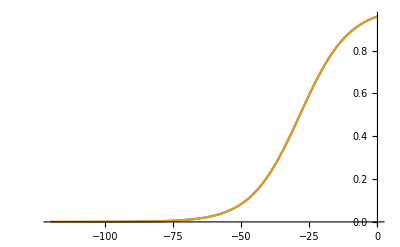

```mathematica
Plot[{(alpha[v]/beta[v])/(1+alpha[v]/beta[v]),1/(1+ⅇ^(-(d[v]-Subscript[𝔳, naha])/Subscript[𝔳, nasp]))}//Evaluate,{v,-120,0}]//Show
```

Matches exactly!

### Dynamics of postsynaptic conductances

#### AMPA conductance: α[t,i]

An alpha function models this conductance’s time-dependence:

```mathematica
T=7 ms;  (* set unit of time to interspike interval *)
Subscript[τ, 0]=(3 ms)/T; (* time-constant *)
α[t_,i_]=(t- i)/Subscript[τ, 0]^2 HeavisideTheta[t-i](Exp[-(t- i)/Subscript[τ, 0]]);
```

Normalizing its peak to unity yields:

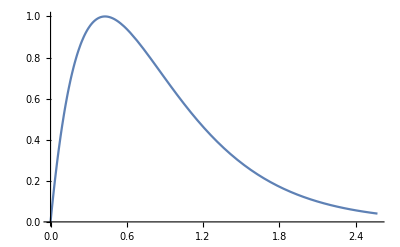

```mathematica
tpks=FindRoot[D[α[tpk,0]/.HeavisideTheta[_]->1,tpk]==0,{tpk,Subscript[τ, 0]}];α[t_,i_]=α[t,i]/α[tpk,0]/.tpks;
SetOptions[Plot, PlotRange->Full,PlotStyle->Automatic];
Plot[α[t,0],{t,0,6 Subscript[τ, 0]}]
```

Responses to periodic spikes 7-ms apart:

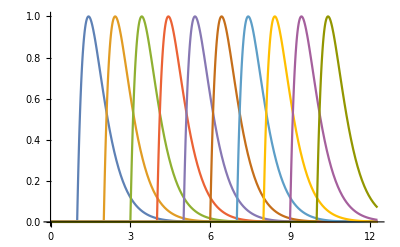

```mathematica
ss=10;Plot[Table[α[t,i],{i,1,ss}]//Evaluate,{t,0,ss+1 +3 Subscript[τ, 0]},PlotPoints->150]
```

#### NMDA conductance: β[t,i]

An exponential rise with time-constant τ_1 and a triple-exponential decay with time-constants τ_2, τ_3, and τ_4 models this conductance’s time-dependence. A linear fit of τ_1’s voltage-dependence [Tank et al. 2008] measured at 28.5^◦C [D’Angelo et al. 1994] and multimodal analysis of single-receptor currents [Iacobucci & Popescu 2017] measured at 23.0^◦C [Popescu et al. 2004], adjusted to 35.0^◦C with q_10=3, yields:

```mathematica
Subscript[A, τ][C_]:=1/3^((35-C)/10.0);
Subscript[τ, 1]=(Subscript[A, τ][28.5])/T(2.915ms -0.004125 ms/mV(-70mV));
{Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4]}=(Subscript[A, τ][23.0])/T{47.0ms,214.0ms,1390.0ms};
{Subscript[τ, 1],Subscript[τ, 2],Subscript[τ, 3],Subscript[τ, 4]}T
```

{1.56866 ms,12.5763 ms,57.2622 ms,371.937 ms}

To maximize AMPA’s efficacy, as explained below, τ_1was adjusted to

```mathematica
Subscript[τ, 1]=(1.4 ms)/T;
```

Scaling the τ_2 exponential by ϕ=0.5 relative to the τ_3 and τ_3 exponentials yields:

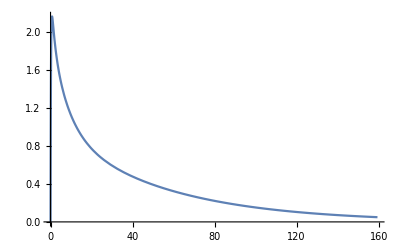

```mathematica
ϕ=0.5;β[t_,i_]=HeavisideTheta[t-i] (ϕ Exp[-(t-i)/Subscript[τ, 2]]+ Exp[-(t-i)/Subscript[τ, 3]]+Exp[-(t-i)/Subscript[τ, 4]]-(ϕ+2)Exp[-(t-i)/Subscript[τ, 1]]);
Plot[β[t,0],{t,0,3 Subscript[τ, 4]}]
```

Responses to periodic spikes 7-ms apart (T=1):

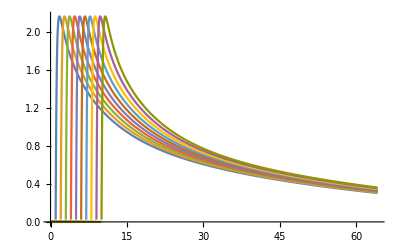

```mathematica
Plot[Table[β[t,i],{i,1,ss}]//Evaluate,{t,0,ss+1+Subscript[τ, 4]},PlotRange->Full,PlotPoints->500]
```

With NMDA’s rise-constant τ_1=(1.4ms)/(7ms)=0.2, two adjacent segments’ NMDA conductances g_nv(t) (blue) and g_nu(t) (orange) are equal when the second’s AMPA conductance  g_au(t) (green) peaks . That maximises AMPA’s efficacy. Normalizing β[t,i] to unity at this time t_eq=t_pk yields

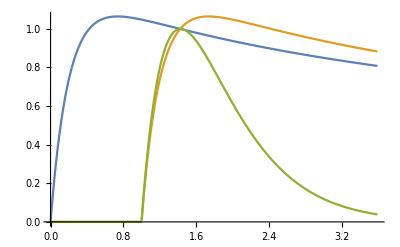

```mathematica
β[t_,i_]=β[t,i]/β[teq,0]/.FindRoot[ β[teq,0]==  β[teq,1],{teq,1+2 Subscript[τ, 1]}];
Plot[{β[t,0], β[t,1],α[t,1]},{t,0,2 Subscript[τ, 2]}]
```

At this time, the phase portrait looks as before:

## Analysis and simulation

### Spineless Dendrite

#### vdnuup[{v,u},{dv,du},g_pk]

Given names {v,u} for voltages in adjacent dendrite segments {v[t],u[t]}, expressions {dv,du} for their temporal derivatives {v̇[v[t],u[t]],u̇[v[t],u[t]]}, and a value gpk for their peak active conductances g_pk, solve for the segments’ down and up voltages v_dn and u_up:

v_dn – Solve dv==0 with {u->v_dn,v->v_dn, g_v->0}

u_up– Solve du==0 with  {u->u_up,v->u_up,g_u->g_pk}

```mathematica
vdnuup[{v_,u_},{dv_,du_} ,gpk_]:= (* evaluates dv/.gv->0 and du/.gu->gpk *)
Module[{veq,vdn,ueq,uup}, (* local variables *)
(* Solve for v=Subscript[v, dn] with neighbors at the same voltage: Subscript[u, up]-Subscript[v, dn]-[Subscript[v, dn]]-Subscript[v, dn] *)
veq=0==dv/.{u[t]->Subscript[v, dn],v[t]->Subscript[v, dn],gv->0};
vdn=NSolve[veq,Subscript[v, dn],Reals][[1,1]]; (* indexes {{Subscript[v, dn]->Subscript[v, 1]}} *)
(* Solve for u=Subscript[u, up] with neighbors at the same voltage: Subscript[u, up]-[Subscript[u, up]]-Subscript[u, up]-Subscript[v, dn] *)
ueq=0==du/.{u[t]->Subscript[u, up],v[t]->Subscript[u, up],gu->gpk};
uup=NSolve[ueq,Subscript[u, up],Reals][[-1,1]]; (* indexes {{Subscript[u, up]->Subscript[u, 1]},{Subscript[u, up]->Subscript[u, 2]},{Subscript[u, up]->Subscript[u, 3]}}, Subscript[u, 1]<Subscript[u, 2]<Subscript[u, 3] *)
{vdn,uup} (* return {Subscript[v, dn]->Subscript[v, 1],Subscript[u, up]->Subscript[u, 3]} *)
]
```

#### PhasePortraitvu[dvdu,{v,u}]

StreamPlot’s trajectories and ParametricPlot’s nullclines of two adjacent dendrite segments, given expressions {dv,du} for their temporal derivatives {v̇[v[t],u[t]],u̇[v[t],u[t]]} and names {v,u} for  their state variables {v[t],u[t]}. Also highlights separatrices (in cyan) and close-by trajectories (in magenta and green). Four steps are involved:

Guess values of v[t] and u[t] at rest (v_dn), threshold (v_th), and plateau (u_up) are  e_inh, 1/2(𝔳_iha+𝔳_nha), and e_exc, respectively.

Search for fixed-points with FindRoot starting from these starting from these points.

Linearize the system at each fixed-point found and identify saddle points.

Highlight streamlines through each saddle point and four points near it.

```mathematica
(* Ensure the points satisfy {0,0}=={dv,du} to attend to these warnings *)
Off[FindRoot::lstol] (* line step doesn't decrease merit function *);
Off[FindRoot::cvmit] (* failed to converge after 100 iterations *); 
(* Note that NSolve[Reals] gets stuck in this 2-D case. *)
```

```mathematica
PhasePortraitvu[dvdu_,{v_,u_}]:= (* dvdu = {v̇[v[t],u[t]],u̇[v[t],u[t]]} *)
Module[{vnl,unl,dnthup,fpl,fps,eigens,sdls,Q1,Q2,Δ,ξ,sepa,quad},(* local variables *)
(* solve for v and u nullclines *)
vnl={v[t],u[t]/.Solve[0==dvdu[[1]],u[t]][[1]]};(* vnl={v,u[v]} *)
unl={v[t]/.Solve[0==dvdu[[2]],v[t]][[1]],u[t]};(* unl={v[u],u} *)
(* Guess values of v[t] and u[t] at fixed points *)
dnthup={Subscript[e, inh],(Subscript[𝔳, iha]+Subscript[𝔳, nha])/2,Subscript[e, exc]}//N;
(* Start FindRoot from these locations and delete duplicated points *)
fpl=DeleteDuplicates[{v[t],u[t]}/.
FindRoot[Thread[vnl==unl],{{v[t],u[t]},#}ᵀ]&/@Join@@Outer[List,dnthup,dnthup],
{p1,p2}|->Chop[(p1-p2).(p1-p2)]==0];
(* Select points {Subscript[p, 1],Subscript[p, 2],...} that satisfy {0,0}=={dv,du}/.{u,v}->Subscript[p, i] to numerical precision: *)
fps=Select[fpl,Chop[dvdu/.Thread[{v[t],u[t]}->#]]=={0,0}&];
(* Linearize {dv[v,u],du[v,u]} at these points to obtain their eigensystems:
{{{Subscript[λ, 1,1],Subscript[λ, 1,2]},{Subscript[e, 1,1],Subscript[e, 1,2]},Subscript[p, 1]},{{Subscript[λ, 2,1],Subscript[λ, 2,2]},{Subscript[e, 2,1],Subscript[e, 2,2]},Subscript[p, 2]},...}, |λ_([.],1)| > |λ_([.],2)| *)
eigens=Append[#][Eigensystem[Grad[dvdu,{v[t],u[t]}]/.Thread[{v[t],u[t]}->#]]]&/@fps;
(* Select saddle points: If Subscript[p, i] is a saddle point, then Subscript[λ, i,1] Subscript[λ, i,2] < 0. *)
sdls=Select[eigens,Times@@#[[1]]<0&]; 
(* For Subscript[Q, 1]={{+1,+1},{+1,-1}} and Subscript[Q, 2]={{+1,+1,+1,+1},{+1,+1,-1,-1},{+1,-1,+1,-1}}ᵀ: 
– {Subscript[a, 1],Subscript[a, 2]}=Subscript[Q, 1].{Subscript[p, i],Subscript[Δe, i,1]} lie ±Δ from Subscript[p, i], 
   on its separatrix and on either side of its nullcline.
– {Subscript[b, 1],Subscript[b, 2],Subscript[b, 3],Subscript[b, 4]}=Subscript[Q, 2].{Subscript[p, i],Subscript[Δe, i,1],Subscript[ξe, i,2]} lie {±Δ,±ξ} from Subscript[p, i],     
  in quadrants its separatrix and nullcline define. *) 
Q1={{+1,+1},{+1,-1}};
Q2={{+1,+1,+1,+1},{+1,+1,-1,-1},{+1,-1,+1,-1}}ᵀ;{Δ,ξ}={0.025,0.05}(-Subtract@@Subscript[v, range]);
sepa=Apply[({λ,e,p}|->Q1.{p,Δ e[[1]]}),sdls,{1}];
quad=Apply[({λ,e,p}|->Q2.{p,Δ e[[1]],ξ e[[2]]}),sdls,{1}];
SetOptions[ParametricPlot,
PlotRange->{Subscript[v, range],Subscript[u, range]},Frame->True,AspectRatio->1,
FrameLabel->{Style[v,"Output",FontColor->Blue],Style[u,"Output",FontColor->Red]}];
SetOptions[StreamPlot,
StreamColorFunction->None,StreamStyle->Orange,StreamScale->Full];
Show[{ (* plot v and u nullclines *)
ParametricPlot[vnl,Prepend[Subscript[v, range],v[t]]//Evaluate,PlotStyle->{Blue}],
ParametricPlot[unl,Prepend[Subscript[u, range],u[t]]//Evaluate,PlotStyle->{Red}],
(* plot phase portrait *)
StreamPlot[dvdu,Prepend[Subscript[v, range],v[t]]//Evaluate,Prepend[Subscript[u, range],u[t]]//Evaluate,
(* highlight separatrices and trajectories near saddles *)
StreamPoints->Join[
Join@@Map[{#,Cyan}&,sepa,{2}],
Join@@Map[{#,{Magenta,Green,Magenta,Green}}ᵀ&,quad],
{Automatic}]]
}]
]
```

#### Simulatevu[dvdu,{v,u},t_m]

NDSolve’s for two adjacent segments’ temporal responses {v[t],u[t]} for t_m units of time (set globally by T), given expressions for their temporal derivatives {v̇[v[t],u[t]],u̇[v[t],u[t]]} and names of their state variables {v,u}.

```mathematica
Simulatevu[dvdu_,{v_,u_},tm_]:= (*  dvdu = {v̇[v[t],u[t]],u̇[v[t],u[t]]} *)
Module[{dot,vnl,unl,ic,deqs,sol}, (* local variables *)
(* Search for{Subscript[v, dn],Subscript[u, dn]} starting from low end of ranges of v and u. *)
ic=FindRoot[Thread[{0,0}==dvdu]/.t->0,
{{v[0],Subscript[v, range][[1]]},{u[0],Subscript[u, range][[1]]}}]/.Rule->Equal;
(* Initialize to {Subscript[v, dn],Subscript[u, dn]} and integrate {v̇[t],u̇[t]} to obtain {v[t],u[t]}. *)
deqs=ic~Join~Thread[{v'[t],u'[t]}==dvdu];
sol=NDSolve[deqs,{v[t],u[t]},{t,0,tm}];
(* Plot v[t] and u[t]. *)
SetOptions[Plot,PlotRange->{Min@@#1,Max@@#2}&@@Transpose[{Subscript[v, range],Subscript[u, range]}],
PlotStyle->{Blue,Red}];
Plot[Evaluate[{v[t],u[t]}/.sol],{t,0,tm}] (* Unlabeled axes keep panels compact *)
]
```

#### Options for plots

```mathematica
SetOptions[StreamPlot,
StreamColorFunction->None,StreamStyle->Orange,StreamScale->Full,PerformanceGoal->"Quality"
];
SetOptions[ParametricPlot,
PlotRangePadding->None,AspectRatio->1,Frame->True,AspectRatio->1,GridLines->{{1},{1}}
];
```

### Spiny Dendrite

#### dvdu[{v,u},{ν,υ},{g_nv,g_nu},{g_av,g_au},g_ki]

Returns expressions for temporal derivatives {v̇,u̇} of spine-head voltages in two adjacent segments, given names of spine-head voltages {v,u} and dendrite-shaft voltages {ν,υ}, instantaneous values {g_nv,g_nu} , {g_av,g_au} , and g_ki of NMDA, AMPA , and KIR synaptic conductances.

```mathematica
(* {v,u}->{𝓋,𝓊} & {ν,υ}->{γ,μ}: these are not values but rather names *)
dvdu[{𝓋_,𝓊_},{γ_,μ_},{ℊ𝓃𝓋_,ℊ𝓃𝓊_},{ℊ𝒶𝓋_,ℊ𝒶𝓊_},ℊ𝓀𝒾_]=
(* returns { 𝓋̇[𝓋[t],γ[t]], 𝓊̇[𝓊[t],μ[t]] } *)
τdvudt/.{v->𝓋,u->𝓊,ν->γ,υ->μ,Subscript[g, ki]->ℊ𝓀𝒾,Subscript[g, nv]->ℊ𝓃𝓋,Subscript[g, nu]->ℊ𝓃𝓊,Subscript[g, av]->ℊ𝒶𝓋,Subscript[g, au]->ℊ𝒶𝓊};
```

#### dνdυ[{v,u},{ν,υ},g_na,g_kv,g_nm,g_ki]

Returns expressions for temporal derivatives {ν̇,υ̇} of dendrite-shaft voltages {ν[t],υ[t]} in two adjacent segments and linear approximations {ν_lin,υ_lin} for {ν[t],υ[t]} at equilibrium, given names of spine-head voltages {v,u} and dendrite-shaft voltages {ν,υ}, instantaneous values g_na and g_kv of voltage-sensitive Na^+ and K^+ conductances, and peak values g_nm and g_ki of NMDA and KIR  conductances. Passing these conductances to νdnυup returns υ_up and ν_dn, the up and down dendrite-shaft voltage (see next subsection).

```mathematica
dνdυ[{v_,u_},{ν_,υ_},ℊ𝓃𝒶_,ℊ𝓀𝓋_,ℊ𝓃𝓂_,ℊ𝓀𝒾_]:=
Module[{τdνdυ,dν,dυ,dνl,dυl},
τdνdυ=τdνυdt/.{ℓ->(Subscript[ℒ, spiny]/s),Subscript[g, prx]->Subscript[g, ser][ℊ𝓀𝒾,Subscript[ℒ, spiny]/s],Subscript[g, dis]->Subscript[g, ser][ℊ𝓃𝓂,Subscript[ℒ, spiny]/s]};
{{dν,dυ},{dνl,dυl}}=τdνdυ/.νdnυup[  (* solves for Subscript[ν, dn] and Subscript[υ, up] *)
 {ν,υ},τdνdυ/.{Subscript[g, na]->ℊ𝓃𝒶,Subscript[g, kv]->ℊ𝓀𝓋},{v,u},dvdu[{v,u},{ν,υ},{0,ℊ𝓃𝓂},{0,0},ℊ𝓀𝒾]
]/.{{Subscript[g, na]->ℊ𝓃𝒶,Subscript[g, kv]->ℊ𝓀𝓋},{Subscript[g, na]->0,Subscript[g, kv]->0}};
(* return { {ν̇[v[t],ν[t],υ[t]],υ̇[u[t],υ[t],ν[t]]},
          {Subscript[ν, lin][v[t],u[t]],    Subscript[υ, lin][v[t],u[t]]}} *)
{{dν,dυ},{ν[t],υ[t]}/.Solve[{0==dνl,0==dυl},{ν[t],υ[t]}][[1]] }
]
```

Notice that this function substitutes  {g_na->0,g_kv->0} to approximate {ν_∞[v,u],υ_∞[v,u]} linearly and returns expressions for {ν_lin[v,u],υ_lin[v,u]} as well as {ν̇[v[t],ν[t],υ[t]],υ̇[u[t],ν[t],υ[t]]}.

#### νdnυup[{ν,υ},{dν,dυ},{v,u},{dv,du},g_pk]

Given names {ν,υ} of dendrite-shaft voltages {ν[t],υ[t]} and expressions {dν,dυ} for their temporal derivatives  {ν̇[t],υ̇[t]]} as well as names {v,u} of spine-head voltages {v[t],u[t]} and expressions {dv,du} for their temporal derivatives {v̇[t], u̇[t]}, solve {dν==0,dv==0} to find ν_dn and {dυ==0,du==0} to find υ_up. Do so by starting FindRoot at e_inh and e_exc, respectively. Note that, NSolve[Reals] gets stuck even in these 1-D cases.

```mathematica
νdnυup[{ν_,υ_},{dν_,dυ_},{v_,u_},{dv_,du_} ]:= 
Module[{dνdn,νdn,dυup,υup}, (* local variables *)
(* Solve for ν=Subscript[ν, dn] with neighbors at the same voltage: Subscript[υ, up]-Subscript[ν, dn]-[Subscript[ν, dn]]-Subscript[ν, dn] *)
dνdn={dν,dv}/.{ν[t]->Subscript[ν, dn],υ[t]->Subscript[ν, dn]}; (* start search at Subscript[e, inh] *)
νdn=FindRoot[Thread[{0,0}==dνdn],{{Subscript[ν, dn],Subscript[e, inh]},{v[t],Subscript[e, inh]}}][[1]]; 
(* Solve for υ=Subscript[υ, up] with neighbors at the same voltage: Subscript[υ, up]-[Subscript[υ, up]]-Subscript[υ, up]-Subscript[v, dn] *)
dυup={dυ,du}/.{υ[t]->Subscript[υ, up],ν[t]->Subscript[υ, up]}; (* start search at Subscript[e, exc] *)
υup=FindRoot[Thread[{0,0}==dυup],{{Subscript[υ, up],Subscript[e, exc]},{u[t],Subscript[e, exc]}}][[1]]; 
{νdn,υup} (* return {Subscript[ν, dn]->Subscript[ν, root],Subscript[υ, up]->Subscript[υ, root]} *)
]
```

#### νυ∞[{ν,υ},{dν,dυ},{ν_lin,υ_lin}]

Given names {ν,υ} of dendrite-shaft voltages {ν[t],υ[t]}, expressions {dν,dυ} for their temporal derivatives  {ν̇[t],υ̇[t]]}, and linear approximations {ν_lin[∞],υ_lin[∞]} for their equilibrium values, start FindRoot there to estimate {ν[∞],υ[∞]} numerically.

```mathematica
νυ∞[{ν_,υ_},{dν_,dυ_},{νl_,υl_}]:={ν[t],υ[t]}/.FindRoot[{dν,dυ},{{ν[t],νl},{υ[t],υl}}]
```

#### SpineDendriteMap[{dν,dυ},{ν_l,υ_l},{ν_r,υ_r},{v_r,u_r}]

Given expressions {dν,dυ} for temporal derivatives {ν̇[t],υ̇[t]]} of dendrite-shaft voltages {ν[t],υ[t]}, linear approximations {ν_l,υ_l} for {ν[∞],υ[∞]}, and ranges {ν_r,υ_r} and {v_r,u_r} for {ν[t],υ[t]} and {v[t],u[t]}, call νυ∞ to estimate {ν[∞],υ[∞]} numerically and ParametricPlot this map from {v[t],u[t]} to {ν[∞],υ[∞]}.

```mathematica
SpineDendriteMap[{{dν_,dυ_},{νl_,υl_}},{νr_,υr_},{vr_,ur_}]:=
Module[{ν,υ},(* vr={v[t],Subscript[v, min],Subscript[v, max]}, etc *)
{ν,υ}=#[[1,0]]&/@{νr,υr}; (* extract variable names*)ParametricPlot[{νυ∞[{ν,υ},{dν,dυ},{νl,υl}],{νl,υl}},vr,ur,
PlotRange->{Rest@νr,Rest@υr},Mesh->Automatic,MeshStyle->{Blue,Red},GridLines->{{1},{1}},
FrameLabel->{
Style[ν,{"Output",FontColor->Blue, FontFamily->"Greek"}],Style[υ,{"Output",FontColor->Red, FontFamily->"Greek"}]}
]]
```

#### dvdu2D and dvdu4D

StreamPlotvu uses these slightly modified versions of dvdu[{v,u},{ν,υ},g_na,g_kv,g_nm,g_ki].

```mathematica
Off[FindRoot::srect];Off[ReplaceAll::reps];
```

```mathematica
(* differs from dvdu: {ν∞,υ∞} are not names but rather values of {ν[t],υ[t]} *)
dvdu2D[{𝓋_,𝓊_},{ν∞_,υ∞_},{ℊ𝓃𝓋_,ℊ𝓃𝓊_},ℊ𝓀𝒾_]=(* returns { 𝓋̇[𝓋[t],ν∞,υ∞],𝓊̇[𝓊[t],ν∞,υ∞] } *)
τdvudt/.{v->𝓋,u->𝓊,ν[t]->ν∞,υ[t]->υ∞,Subscript[g, nv]->ℊ𝓃𝓋,Subscript[g, nu]->ℊ𝓃𝓊,Subscript[g, av]->0,Subscript[g, au]->0,Subscript[g, ki]->ℊ𝓀𝒾};
```

```mathematica
(* {vt,ut} and {ν∞,υ∞} are values for {v[t],u[t]} and {ν[∞],υ[∞]}, respectively *)
dvdu4D[{vt_,ut_},{ν∞_,υ∞_},{ℊ𝓃𝓋_,ℊ𝓃𝓊_},ℊ𝓀𝒾_]=(* returns { v̇[vt,ν∞,υ∞],u̇[ut,ν∞,υ∞] } *)
τdvudt/.{v[t]->vt,u[t]->ut,ν[t]->ν∞,υ[t]->υ∞,Subscript[g, nv]->ℊ𝓃𝓋,Subscript[g, nu]->ℊ𝓃𝓊,Subscript[g, av]->0,Subscript[g, au]->0,Subscript[g, ki]->ℊ𝓀𝒾};
```

#### dνυdvu[{v,u},{ν,υ},τdνυdt,g_na,g_kv,g_nm,g_ki]

Differentiates an expression τdνυdt for {ν̇[v,u],υ̇[v,u]]} implicitly to obtain the Jacobian, given names of spine-head voltages {v,u} and dendrite-shaft voltages {ν,υ} as well as instantaneous values {g_nv,g_nu} , {g_av,g_au}, and g_ki of NMDA, AMPA, and KIR synaptic conductances.

```mathematica
dνυdvu[{v_,u_},{ν_,υ_},τdνυdt_,ℊ𝓃𝒶_,ℊ𝓀𝓋_,ℊ𝓃𝓂_,ℊ𝓀𝒾_]:=
Module[{dν,dυ,grad,dυdvs,dνdvs,dυdus,dνdus},
{dν,dυ}=Thread[{0,0}==τdνυdt/.{ν[t]->ν[v,u],υ[t]->υ[v,u],x_[t]->x}];
grad=Grad[{dν,dυ},{v,u}]//Simplify;
dυdvs=Solve[grad[[1,1]],Derivative[1,0][υ][v,u]][[1,1]];
dνdvs=Solve[grad[[2,1]]/.dυdvs,Derivative[1,0][ν][v,u]][[1,1]];
dυdvs=dυdvs/.dνdvs;
dυdus=Solve[grad[[1,2]],Derivative[0,1][υ][v,u]][[1,1]];
dνdus=Solve[grad[[2,2]]/.dυdus,Derivative[0,1][ν][v,u]][[1,1]];
dυdus=dυdus/.dνdus;
(* return Jacobian *)
{{Derivative[1,0][ν][v,u]/.dνdvs,Derivative[0,1][ν][v,u]/.dνdus},
{Derivative[1,0][υ][v,u]/.dυdvs,Derivative[0,1][υ][v,u]/.dυdus}}/.{ν[v,u]->ν[t],υ[v,u]->υ[t],Subscript[g, na]->ℊ𝓃𝒶,Subscript[g, kv]->ℊ𝓀𝓋,ℓ->(Subscript[ℒ, spiny]/s),
Subscript[g, prx]->Subscript[g, ser][ℊ𝓀𝒾,Subscript[ℒ, spiny]/s],Subscript[g, dis]->Subscript[g, ser][ℊ𝓃𝓂,Subscript[ℒ, spiny]/s]}
]
```

#### ndvdudνdυ[dvdu,{v,u},dνdυ,{ν,υ},{gv,gu}]

Finds expressions for v and u nullclines in three steps.

v nullcline – Given names {v,u} for voltages in dendrite-shafts of adjacent segments and expressions dvdu for their temporal derivatives {v̇[t],u̇[t]} as well as names{ν,υ} for voltages in spine-heads of these segments and expressions dνdυ for their temporal derivatives {ν̇[t],υ̇[t]}, find {v,u[v]}:

Given dvdu⟦1⟧, an expression for v̇[t], solve dvdu⟦1⟧==0 for ν[t].

Substitute ν[t] into dνdυ⟦1⟧,  an expression ν̇[t], and solve dνdυ⟦1⟧==0  for υ[t].

Substitute ν[t] and υ[t] into  dνdυ⟦2⟧, an expression for υ̇[t], and solve  dνdυ⟦2⟧==0 for u[t].

u nullcline  – And find {v[u],u} by repeating these three steps: solve dvdu⟦2⟧==0 for υ[t],  dνdυ⟦2⟧==0 for ν[t], and dνdυ⟦1⟧==0 for v[t] (i.e., ⟦1⟧↔⟦2⟧).

```mathematica
ndvdudνdυ[dvdu_,{v_,u_},dνdυ_,{ν_,υ_}]:=
Module[{νsol,νυsol,υsol,υνsol},
(* solve for v nullcline: {v,u[v]} *)
νsol=Solve[0==dvdu[[1]],ν[t]][[1,1]];
νυsol={νsol,Solve[0==dνdυ[[1]]/.νsol,υ[t]][[1,1]]};
(* solve for u nullcline: {v[u],u} *)
υsol=Solve[0==dvdu[[2]],υ[t]][[1,1]];
υνsol={υsol,Solve[0==dνdυ[[2]]/.υsol,ν[t]][[1,1]]};
(* return {{v,u[v]},{v[u],u}} & {ν[t],υ[t]} *)
{{{v[t],u[t]}/.Solve[0==dνdυ[[2]]/.νυsol,u[t]][[1,1]],
{v[t],u[t]}/.Solve[0==dνdυ[[1]]/.υνsol,v[t]][[1,1]]},
{{ν[t],υ[t]}/.νυsol,
{ν[t],υ[t]}/.υνsol}}
]
```

#### StreamPlotvu[fvu,{v,u},{vnl,unl}]

StreamPlots trajectories given expressions fvu for temporal derivatives {v̇[v[t],u[t]],u̇[v[t],u[t]]} of voltages {v[t],u[t]} in two adjacent segments, names {v,u} for  their state variables {v[t],u[t]}, and ParametricPlots expressions {vnl,unl} for their nullclines {{v,u[v]},{v[u],u}}.

```mathematica
StreamPlotvu[{ℊ𝓃𝓋_,ℊ𝓃𝓊_},{ℊ𝓃𝓂_,ℊ𝓀𝒾_},{ℊ𝓃𝒶_,ℊ𝓀𝓋_},{vr_,ur_},{νr_,υr_}]:= 
Module[{v,u,ν,υ,dν,dυ,dνl,dυl,νl,υl,dv,du,vnl,unl,νnl,υnl,v∞,u∞,dνdt,dυdt},
{{v,u},{ν,υ}}=Map[#[[1,0]]&,{{vr,ur},{νr,υr}},{2}]; (* variable names *)
{{dν,dυ},{νl,υl}}=dνdυ[{v,u},{ν,υ},ℊ𝓃𝒶,ℊ𝓀𝓋,ℊ𝓃𝓂,ℊ𝓀𝒾];
{dv,du}=dvdu[{v,u},{ν,υ},{ℊ𝓃𝓋,ℊ𝓃𝓊},{0,0},ℊ𝓀𝒾];
{{vnl,unl},{νnl,υnl}}=ndvdudνdυ[{dv,du},{v,u},{dν,dυ},{ν,υ}];
{v∞,u∞}={v[t]/.Solve[dν==0,v[t]][[1]],u[t]/.Solve[dυ==0,u[t]][[1]]}//Simplify;
{dνdt,dυdt}=dνυdvu[{v,u},{ν,υ},τdνυdt,ℊ𝓃𝒶,ℊ𝓀𝓋,ℊ𝓃𝓂,ℊ𝓀𝒾].dvdu4D[{v∞,u∞},{ν[t],υ[t]},{ℊ𝓃𝓂,ℊ𝓃𝓂},ℊ𝓀𝒾];
GraphicsRow[{
SetOptions[ParametricPlot,PlotRange->Rest/@{vr,ur},FrameLabel->{Style[v,"Output",FontColor->Blue],Style[u,"Output",FontColor->Red]}];Show[ParametricPlot[vnl,vr,PlotStyle->Blue],ParametricPlot[unl,ur,PlotStyle->Red],
StreamPlot[dvdu2D[{v,u},νυ∞[{ν,υ},{dν,dυ},{νl,υl}],{ℊ𝓃𝓋,ℊ𝓃𝓊},ℊ𝓀𝒾],vr,ur]],
SetOptions[ParametricPlot,PlotRange->Rest/@{νr,υr},FrameLabel->{
Style[ν,{"Output",FontColor->Blue, FontFamily->"Greek"}],Style[υ,{"Output",FontColor->Red, FontFamily->"Greek"}]}];
Show[ParametricPlot[νnl,vr,PlotStyle->Blue],ParametricPlot[υnl,ur,PlotStyle->Red],
StreamPlot[{dνdt,dυdt},νr,υr]]
}]
]
```

#### Hvu[ν_t,υ_t]

Total energy {v,u,Hvu[ν,υ]} – Compute total energy assuming dendrite shafts are at equilibrium ({dν/dt,dυ/dt}={0,0}).

```mathematica
Hvu[νt_,υt_]:={
vs,us,1/2((vs-νt)^2+(us-υt)^2+(l/s)^2(υt-νt)^2+gprx(νd-νt)^2+gdis(υp-υt)^2)+
Gk[νt]+Gna[νt]+Gk[υt]+Gna[υt]+Gi[vs]+Gn[vs]+Gi[us]+Gn[us]
}/.{
vs->νt-(l/s)^2(υt-νt)-gprx(νd-νt)-gk Subscript[f, sig][νt,Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]-gna Subscript[f, sig][νt,Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]],us->υt-gdis(υp-υt)-(l/s)^2(νt-υt)-gk Subscript[f, sig][υt,Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]-gna Subscript[f, sig][υt,Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]}
```

#### Options for plots

```mathematica
SetOptions[ListStreamPlot,
StreamColorFunction->None,StreamStyle->Orange,StreamScale->Full,StreamMarkers->Automatic,StreamPoints->Fine,PerformanceGoal->"Quality",Frame->False,PlotRangePadding->None
];
SetOptions[ListPlot3D,
BoxRatios->{1,1,0.66},Lighting->Automatic,ClippingStyle->None,MaxPlotPoints->100,Axes->True, PlotTheme-> Automatic,PerformanceGoal->"Quality"(*,PlotTheme->"ThickSurface"*)
];
SetOptions[ListContourPlot,
PlotRange->{vr,ur},ContourStyle->None,PerformanceGoal->"Quality",PlotLegends->Automatic,
Frame->False(*,FrameLabel->{v,u}*)
];
(* These are no longer used *)
SetOptions[ContourPlot,
PlotRange->{νr,υr},PerformanceGoal->"Quality",PlotLegends->Automatic,Frame->False,PlotRangePadding->None(*,FrameLabel->{ν,υ}*)
];
SetOptions[Plot3D,
PerformanceGoal->"Quality",BoxRatios->{1,1,0.5},PlotRange->{-0.2,0.6},PlotPoints->100,PlotTheme->"ThickSurface",ClippingStyle->None,Axes->False,ViewPoint->{-1.0,-1.0,1.25},Boxed->False
];
```

## Spineless dendrite

### Equations of motion

Voltages u[t] and v[t] of adjacent dendrite segments satisfy:

```mathematica
τdudt =(Subscript[e, lk]-u[t])+ℓ^2(v[t]-u[t])+Subscript[g, dis](Subscript[u, up]-u[t])+Subscript[g, au](Subscript[e, exc]-u[t])+Subscript[g, ki] Subscript[f, sig][u[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, nu] Subscript[f, sig][u[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[g, k] Subscript[f, sig][u[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, na] Subscript[f, sig][u[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]];
τdvdt=(Subscript[e, lk]-v[t])+ℓ^2(u[t]-v[t])+Subscript[g, prx](Subscript[v, dn]-v[t])+Subscript[g, av](Subscript[e, exc]-v[t])+Subscript[g, ki] Subscript[f, sig][v[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, nv] Subscript[f, sig][v[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[g, k] Subscript[f, sig][v[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, na] Subscript[f, sig][v[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]];
```

These terms model:

Passive conductances – 1 unit for leak, g_[au,av] units for AMPA synapses, and ℓ^2 units for intracellular fluid between adjacent slices. If a segment of  lumps s slices together, then ℓ->ℓ/s.

Active currents – f_sig[v,e_ch,𝔳_ha,𝔳_sp] multiplies a driving-force e_ch-v by a sigmoid that e-folds from v to v+𝔳_sp and equals 1/2 when v=𝔳_ha. By definition,  df_sig/dv=1 when v=e_ch, so its conductance is 1 unit. Hence, multiplying by g_ki, g_[nu,nv], g_k , and g_na yields current conducted by KIR, NMDA, high-threshold K^+, and persistent Na^+ channels, respectively, provided e_ch, 𝔳_sp, and 𝔳_ha are set appropriately.

Bistable states – u_up is the plateau potential (up) and v_dn is the rest potential (down).

Set parameter values:

```mathematica
s=3; (* number of slices per segment *)
T=7 ms; (* unit of time *)
gnp=300;gip=575;gnap=3.0;gkp=0.3; (* active conductances *)
gdis=Subscript[g, par][gnp,Subscript[ℒ, den]/s];gprx=Subscript[g, par][gip,Subscript[ℒ, den]/s];  (* for infinite cable *)
{dv,du}={τdvdt,τdudt}/(Subscript[τ, den]/T)/.{ℓ->(Subscript[ℒ, den]/s),Subscript[g, dis]->gdis,Subscript[g, prx]->gprx,Subscript[g, au]->gau,Subscript[g, av]->gav,Subscript[g, ki]->gip,
Subscript[g, nu]->gnu,Subscript[g, nv]->gnv,Subscript[g, k]->gkp,Subscript[g, na]->gnap};
dvdu[{v_,u_},{gnv_,gnu_},{gav_,gau_}]=(* vdnuup evaluates {du,du}/.{gv->gnp,gu->gnp} *)
{dv,du}/.vdnuup[{v,u},{dv,du}/.{gnv->gv,gnu->gu,gav->0,gau->0},gnp];
```

### Phase portraits

Increasing NMDA conductances from a minimal to a maximal level increases the number of stable points from one to three, between which lie two saddle points:

```mathematica
{min,max}={0.1,1.0}gnp;  (* minimal & maximal NMDA conductances *)
Subscript[v, range]={0.1,2.0}; Subscript[u, range]={0.3,2.2};
```

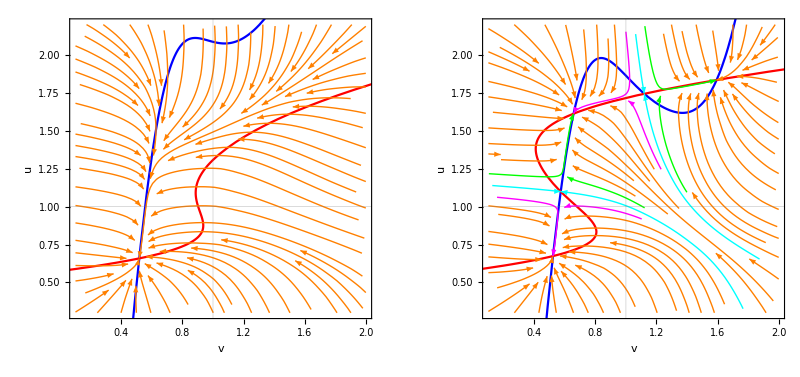

```mathematica
GraphicsRow[{
PhasePortraitvu[dvdu[{v,u},{min,min},{0,0}],{v,u}],
PhasePortraitvu[dvdu[{v,u},{max,max},{0,0}],{v,u}]
}]
```

Left – Minimal NMDA conductances: u’s nullcline (red) and v’s nullcline (blue) intersect to create a stable point (down-down). 
Right – Maximal NMDA conductances: u’s nullcline (red) and v’s nullcline (blue) intersect to create three stable-points (down-down, down-up, and up-up). These stable points’ basins of attraction are defined by two separatrices (cyan) that pass through two saddle points (down-threshold and threshold-up). Borderline trajectories (magenta or green) first converge to and then diverge from these saddle points.

Including minimal g_nu cum maximal g_nv and vise versa yields all four possible combinations:

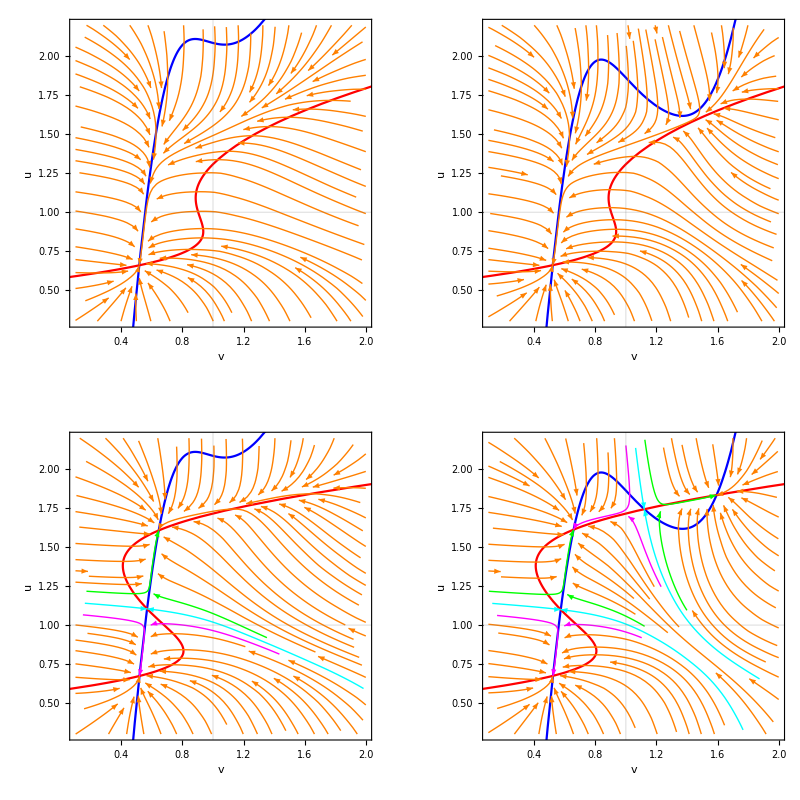

```mathematica
GraphicsGrid[Map[PhasePortraitvu[dvdu[{v,u},#,{0,0}],{v,u}]&,
{{{min,min},{max,min}},{{min,max },{max,max}}},{2}]]
```

Upper right – Minimal g_nu cum maximal g_nv: Down-down is still the only fixed point.
Lower left – Maximal g_nu cum minimal g_nv: Down-up stable-point appears together with the saddle point that lies between down-up and down-down.

### Simulations

Tweaking peak AMPA conductances {g_av,g_au} yielded the smallest values that can trigger a transition from down-down to down-up or up-up and from down-up to up-up. Here are plots of v(t) in blue and u(t) in red:

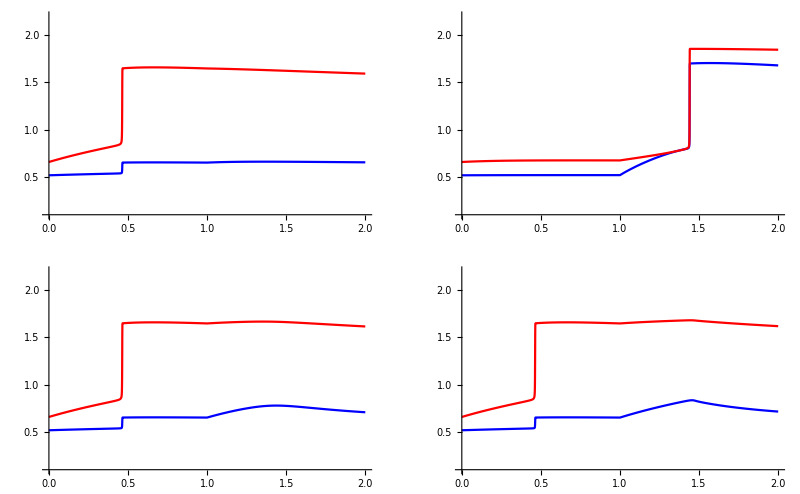

```mathematica
GraphicsGrid[Map[
Simulatevu[dvdu[{v,u},{gnp β[t,1],gnp β[t,0]},{#[[1]]α[t,1], #[[2]]α[t,0]}],
{v,u},2.0]&,
{{{0,16.8},{70.2,0}},{{16.8,16.8},{18.6,16.8}}},{2}]]
```

Upper-left –  {0.0,16.8} triggers a down-down to down-up transition because u’s other neighbor is up.
Lower-left – {16.8,16.8} doesn’t trigger a down-down to up-up transition because v’s other neighbor is down. 
Upper-right – {70.2,0.0} triggers down-down to up-up transition.
Lower-right – {18.6,16.8} triggers down-up to up-up transition because flipping u quarters the threshold.

In all four cases, the system transitions back to down-down after about 5 units of time:

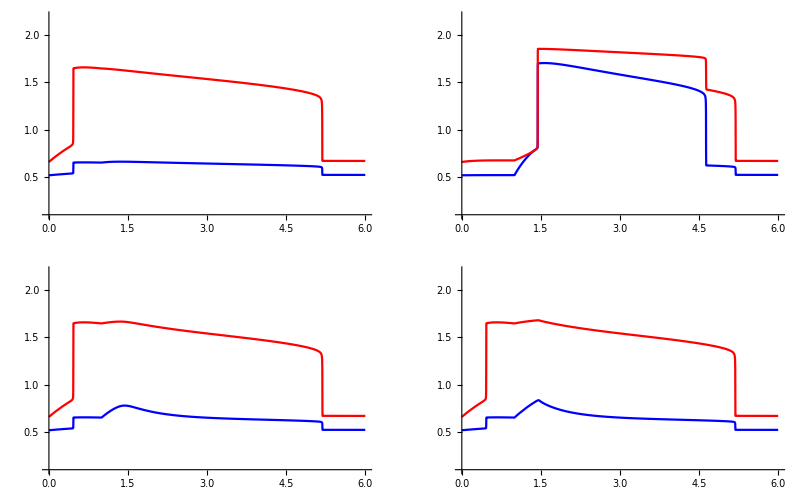

```mathematica
GraphicsGrid[Map[
Simulatevu[dvdu[{v,u},{gnp β[t,1],gnp β[t,0]},{#[[1]]α[t,1], #[[2]]α[t,0]}],
{v,u},6.0]&,
{{{0,16.8},{70.2,0}},{{16.8,16.8},{18.6,16.8}}},{2}]]
```

Upper-left – Transitions from down-up back to down-down.
Lower-left –  Transitions from down-up back to down-down. 
Upper-right – Transitions from up-up back to down-down.
Lower-right – Transitions from down-up back to up-up.

## Spiny dendrite

### Cable properties

Membrane capacitance 𝒸_spi of a spine’s head is derived from its radius  𝓇_spi and membrane capacitance 𝒸_nck and axial conductance 𝒢_nck of a spine’s neck are derived from its radius 𝓇_nck and length ℓ_nck.

```mathematica
(* head *)
Subscript[𝓇, spi]=0.288μm; (* 0.1 μm^3 volume [Lichtman'15] *)
Subscript[𝒮, spi]=4π Subscript[𝓇, spi]^2;Subscript[𝒸, spi]=Subscript[𝒮, spi] Subscript[c, m]; (* capacitance *)
(* neck *)
{ Subscript[𝓇, nck],Subscript[ℓ, nck]}={0.0625,1.8}μm; (* L5 [Lichtman'15] *)
Subscript[𝒮, nck]=2π Subscript[𝓇, nck] Subscript[ℓ, nck]; Subscript[𝒸, nck]=Subscript[𝒮, nck] Subscript[c, m]; (* capacitance *)
Subscript[𝒜, nck]=π Subscript[𝓇, nck]^2;Subscript[𝒢, nck]=1/Subscript[R, ax] Subscript[𝒜, nck]/Subscript[ℓ, nck](MΩ nS)/10^-3; (* conductance *)
{{"","Slice","Neck","Ratio"},
{"Capacitance",Subscript[𝒸, sli],Subscript[𝒸, nck],Subscript[𝒸, nck]/Subscript[𝒸, sli] },
{"Conductance",Subscript[𝒢, sli],Subscript[𝒢, nck],Subscript[𝒢, nck]/Subscript[𝒢, sli](10^3 pS)/nS},
{"Resistance",Subscript[ℛ, sli],Subscript[ℛ, nck]=1/Subscript[𝒢, nck](MΩ nS)/10^-3,Subscript[ℛ, nck]/Subscript[ℛ, sli]}}//TableForm
```

| Slice | Neck | Ratio
Capacitance | 7.85398 fF | 7.06858 fF | 0.9
Conductance | 18.8496 pS | 1.70442 nS | 90.4225
Resistance | 81.4873 MΩ | 586.709 MΩ | 7.2

While the neck’s capacitance is similar to the slice’s, its axial conductance 𝒢_nck and axial resistance 1/𝒢_nck are 90 and 7.2-fold the slice’s leak conductance 𝒢_sli and axial resistance ℛ_sli, respectively. Since 𝒢_nck≫𝒢_sli, the spiny dendrite model ignores 𝒢_sli. Instead,  𝒢_nck determines its space-constant ℒ_spiny and time-constant τ_spiny:

```mathematica
{Subscript[ℒ, spiny]=1/(√(Subscript[ℛ, sli] Subscript[𝒢, nck]))/.MΩ nS->10^-3 ;{Subscript[τ, spiny],Subscript[τ, head]}={(Subscript[𝒸, sli]+0.5 Subscript[𝒸, nck])/Subscript[𝒢, nck],(Subscript[𝒸, spi]+0.5 Subscript[𝒸, nck])/Subscript[𝒢, nck]}nS/10^-9 10^-15/fF ms/10^-3 1/T } ;{Subscript[ℒ, spiny],{Subscript[τ, spiny],Subscript[τ, head]}T}
```

{2.68328,{0.0066816 ms,0.0081889 ms}}

Relocating NMDA and KIR synapses from dendrite shaft to spine head inserts 𝒢_nck in series with either 𝒢_NMDA or 𝒢_KIR, depending on whether the spine head is plateauing or resting. This synaptic conductance 𝒢_syn modifies the leak conductance of a spiny dendrite cable to 𝒢=(𝒢_syn 𝒢_nck)/(𝒢_syn+𝒢_nck). In units of  𝒢_nck,  g_syn=𝒢_syn/𝒢_nck, g=𝒢/𝒢_nck=g_syn/(g_syn+1), and RG=ℛ_sli 𝒢_nck 𝒢_syn/(𝒢_syn+𝒢_nck)=g/ℒ_spiny^2. Hence, the equivalent conductance g_∞=(𝒢_∞)/𝒢_nck of an infinitely long spiny-dendrite cable is:

```mathematica
Subscript[g, ser][gsyn_,ℓ_]=(gser=gsyn/(gsyn+1); FullSimplify[Subscript[g, ∞][gser/ℓ^2]gser,gsyn>0&&ℓ>0]) (* in units of Subscript[𝒢, nck] *)
```

(gsyn (-1+√(1+(4 (1+gsyn) ℓ^2)/gsyn)))/(2 (1+gsyn))

This yields g_dis=g_ser[g_NMDA] and g_prx=g_ser[g_KIR].

The number of slices s per segment and the multiplicative factor A_g that converts conductances from 𝒢_sli units to 𝒢_nck units are:

```mathematica
s=3; (* number of slices per segment *)
Subscript[A, g]:=a Subscript[𝒢, sli]/Subscript[𝒢, nck] nS/(10^3 pS); (* covert units from Subscript[𝒢, sli] to Subscript[𝒢, nck] *)
(* a rescales uniformly; ":=" ensures Subscript[A, g] updates when a changes. *)
```

### Equations of motion

Let u[t] and v[t] be spine-head voltages and υ[t] and ν[t] be dendrite-shaft voltages in two adjacent segments. Also, let υ_up and ν_dn be dendrite-shaft voltages in their distal and proximal neighbors, respectively. Couple υ[t] to υ_up with g_dis=g_ser[g_NMDA] and couple ν[t] to ν_dn with g_prx=g_ser[g_KIR]. Then, τ_head{v̇[t],u̇[t]} and τ_spiny{ν̇[t],υ̇[t]} are given by:

```mathematica
τdvudt ={
(ν[t]-v[t])+Subscript[g, ki] Subscript[f, sig][v[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, nv] Subscript[f, sig][v[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[g, av](Subscript[e, exc]-v[t]),(υ[t]-u[t])+Subscript[g, ki] Subscript[f, sig][u[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, nu] Subscript[f, sig][u[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[g, au](Subscript[e, exc]-u[t])};
τdνυdt ={
(v[t]-ν[t])+ℓ^2(υ[t]-ν[t])+Subscript[g, prx](Subscript[ν, dn]-ν[t])+Subscript[g, kv] Subscript[f, sig][ν[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, na] Subscript[f, sig][ν[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]],
(u[t]-υ[t])+ℓ^2(ν[t]-υ[t])+Subscript[g, dis](Subscript[υ, up]-υ[t])+Subscript[g, kv] Subscript[f, sig][υ[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, na] Subscript[f, sig][υ[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]};
```

This spiny-dendrite model’s conductances are specified in units of the axial conductance 𝒢_nck of a spine neck, whereas the spineless-dendrite model’s are specified in units of the leak conductance 𝒢_sli of a dendrite slice. Multiplying the spineless model’s conductances by a unit-conversion factor A_g yields the spiny model’s conductances:

```mathematica
gnm:=300 Subscript[A, g];gki:=575 Subscript[A, g];gna:=3.0 Subscript[A, g];gkv:=0.3 Subscript[A, g]; 
(* ":=" updates these when Subscript[A, g] changes. *)
```

A_g is defined such that a global scale-factor a rescales these conductances uniformly (see previous section). They match the spineless dendrite model’s when a=1:

```mathematica
a=1;{Subscript[A, g],gnm,gki,gna,gkv}
```

{0.0110592,3.31776,6.35904,0.0331776,0.00331776}

That is, g_NMDA=3.3 and g_KIR=6.4 in units of 𝒢_nck.

Call this function to express {v̇,u̇} in terms of v[t], u[t], ν[t], and υ[t]:

```mathematica
dvdu[{v,u},{ν,υ},{gnm,gnm},{0,0},gki]
```

{(8.6984 (1/2-v[t]))/(1+ⅇ^(6. (-0.666667+v[t])))+(3.81598 (2-v[t]))/(1+ⅇ^(-4.8 (-1.605+v[t])))-v[t]+ν[t],(8.6984 (1/2-u[t]))/(1+ⅇ^(6. (-0.666667+u[t])))+(3.81598 (2-u[t]))/(1+ⅇ^(-4.8 (-1.605+u[t])))-u[t]+υ[t]}

And call this function to express {ν̇,υ̇} in terms of v[t], u[t], ν[t], and υ[t]:

```mathematica
dνdυ[{v,u},{ν,υ},gna,gkv,gnm,gki]
```

{{v[t]+(0.119536 (1/2-ν[t]))/(1+ⅇ^(-3.52941 (-2+ν[t])))+0.438966 (0.500028-ν[t])+(0.00597294 (2.83333-ν[t]))/(1+ⅇ^(-6.66667 (-1.525+ν[t])))-ν[t]+0.8 (-ν[t]+υ[t]),u[t]+(0.119536 (1/2-υ[t]))/(1+ⅇ^(-3.52941 (-2+υ[t])))+0.391039 (1.84625-υ[t])+(0.00597294 (2.83333-υ[t]))/(1+ⅇ^(-6.66667 (-1.525+υ[t])))+0.8 (ν[t]-υ[t])-υ[t]},{0.248141+0.187544 u[t]+0.513646 v[t],0.420105+0.524881 u[t]+0.187544 v[t]}}

It also substitutes  {g_na->0,g_kv->0} to approximate {ν[∞],υ[∞]} linearly and returns  {ν_lin[v,u],υ_lin[v,u]}.

### Voltage-map form spine to dendrite

SpineDendriteMap visualizes voltage-map from instantaneous spine-head voltages {v[t],u[t]} to equilibrium dendrite-shaft voltages {ν[∞],υ[∞]}. Here’s a map for the default values of g_kv and g_Na:

```mathematica
(* plot ranges *) 
Subscript[vu, range]={{v[t],Subscript[e, inh],Subscript[e, exc]},{u[t],Subscript[e, inh],Subscript[e, exc]}}//N;  
Subscript[νυ, range]={{ν[t],1.1 Subscript[e, inh],0.9125 Subscript[e, exc]},{υ[t],1.5 Subscript[e, inh],1.0125 Subscript[e, exc]}};
```

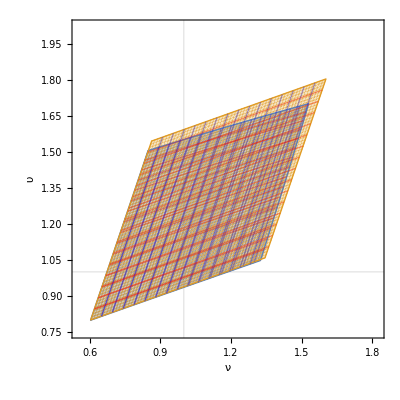

```mathematica
a=1.0;
SpineDendriteMap[dνdυ[{v,u},{ν,υ},gna,gkv,gnm,gki],Subscript[νυ, range],Subscript[vu, range]]
```

Voltage-map {ν[v,u],υ[v,u]} from spine-heads {v,u} to dendrite-shafts {ν,υ} (shaded light blue) and its linear approximation (shaded light orange). A mesh of spine-head voltages {iΔv,jΔu} is mapped to a mesh of dendrite-shaft voltages {ν[iΔv,jΔu],υ[iΔv,jΔu]}. Blue lines trace {ν[iΔv,u],υ[iΔv,u], holding v constant. Red lines trace {ν[v,jΔu],υ[v,jΔu]}, holding  u constant. These maps’ leftward shift is due to voltage decay along the dendrite (i.e. ν[t]<υ[t]).

For their default values, g_kv attenuates more than g_na amplifies and hence the active dendrite’s spine-head voltages are more attenuated than the passive dendrite’s. Zeroing g_na isolates the effect of g_kv and vise versa:

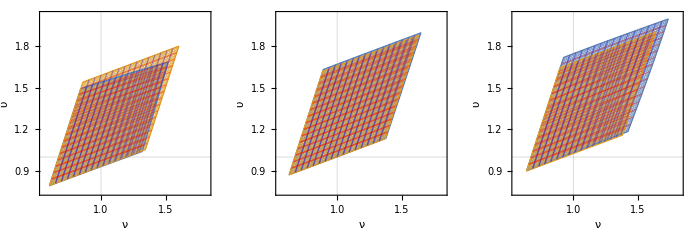

```mathematica
GraphicsRow[SpineDendriteMap[dνdυ[{v,u},{ν,υ},#[[1]],#[[2]],gnm,gki],Subscript[νυ, range],Subscript[vu, range]]&/@ {{0,gkv},{gna,0},{5gna,0}}]
```

Left – {0,g_kv}: Zeroing g_na leaves the active dendrite’s map (light blue) unchanged, confirming that g_kv is dominant. 
Middle –  {g_na,0}: Zeroing g_kv makes the active dendrite’s map match the passive dendrite’s (light orange), implying g_na’s effect is negligible in the default setting. 
Right –  {5 g_na,0}: Increasing g_na fivefold reverses the situation: the active dendrite’s spine-head voltages are now less attenuated the passive dendrite’s.

### Phase portraits

The state of two adjacent segments {{v[t],u[t]},{ν[t],υ[t]}} is reduced to {v[t],u[t]} by assuming {ν[t],υ[t]}≈{ν_∞[v,u],υ_∞[v,u]}. StreamPlotvu plots a 2D phase portrait of {v̇[v[t],u[t]],u̇[v[t],u[t]} and visualizes the mapping from {v[t],u[t]} to {ν[∞],υ[∞]}.

```mathematica
(* plot ranges *) 
Subscript[vu, range]={{v[t],Subscript[e, inh],Subscript[e, exc]},{u[t],Subscript[e, inh],Subscript[e, exc]}}//N;  
Subscript[νυ, range]={{ν[t],1.2 Subscript[e, inh],0.75 Subscript[e, exc]},{υ[t],1.6 Subscript[e, inh],0.85 Subscript[e, exc]}};
```

For the default parameter value, there are four stable points separated by four saddle points and one unstable point.

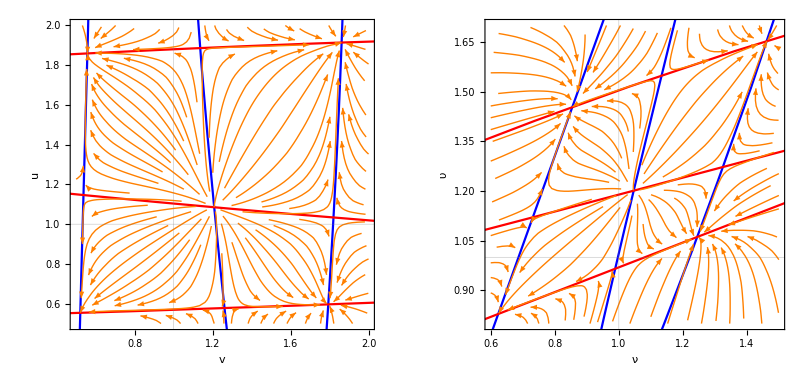

```mathematica
a=1;StreamPlotvu[{gnm,gnm},{gnm,gki},{gna,gkv},Subscript[vu, range],Subscript[νυ, range]]
```

Left – Spine-head space: u’s nullcline (red) and v’s nullcline (blue) intersect to create four stable points (down-down, down-up, up-down, and up-up), four saddle-points (down-threshold, threshold-down, up-threshold, and threshold-up), and one unstable point (threshold-threshold).  
Right – Dendrite-shaft space: Mapping of nullclines and trajectories from spine-head {v,u} to dendrite-shaft {ν,υ} space.

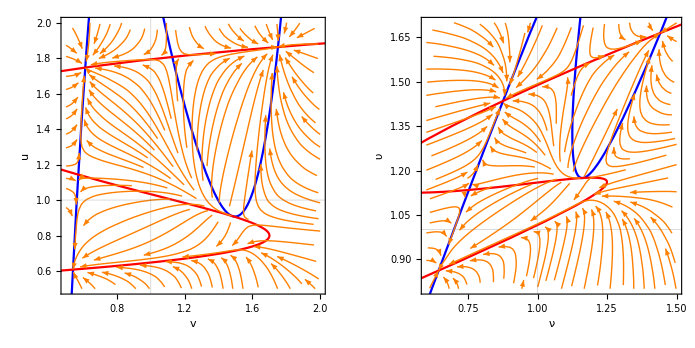

```mathematica
a=1/2;StreamPlotvu[{gnm,gnm},{gnm,gki},{gna,gkv},Subscript[vu, range],Subscript[νυ, range]]
```

Left – Spine-head space: u’s nullcline (red) and v’s nullcline (blue) intersect to create three stable points (down-down, down-up, and up-up), two saddle-points (down-threshold and threshold-up).  
Right – Dendrite-shaft space: Mapping of nullclines and trajectories from spine-head {v,u} to dendrite-shaft {ν,υ} space.

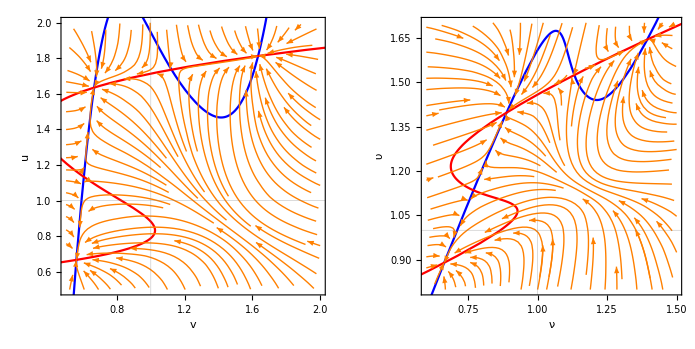

```mathematica
a=1/3;StreamPlotvu[{gnm,gnm},{gnm,gki},{gna,gkv},Subscript[vu, range],Subscript[νυ, range]]
```

Left – Spine-head space: u’s nullcline (red) and v’s nullcline (blue) intersect to create three stable points (down-down, down-up, and up-up), two saddle-points (down-threshold and threshold-up).  
Right – Dendrite-shaft space: Mapping of nullclines and trajectories from spine-head {v,u} to dendrite-shaft {ν,υ} space.

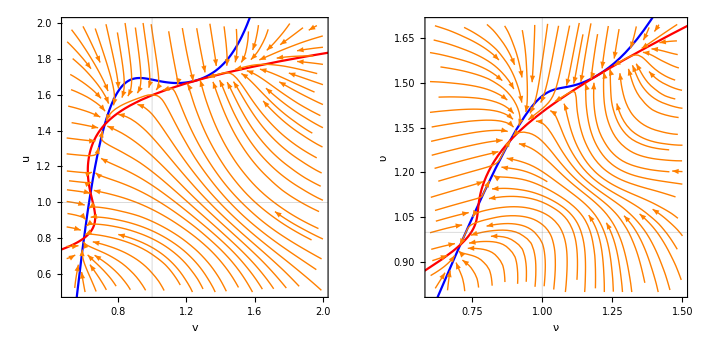

```mathematica
a=11/50;StreamPlotvu[{gnm,gnm},{gnm,gki},{gna,gkv},Subscript[vu, range],Subscript[νυ, range]]
```

Left – Spine-head space: u’s nullcline (red) and v’s nullcline (blue) intersect to create two stable points (down-down and down-up) and one saddle point (down-threshold).  
Right – Dendrite-shaft space: Mapping of nullclines and trajectories from spine-head {v,u} to dendrite-shaft {ν,υ} space.

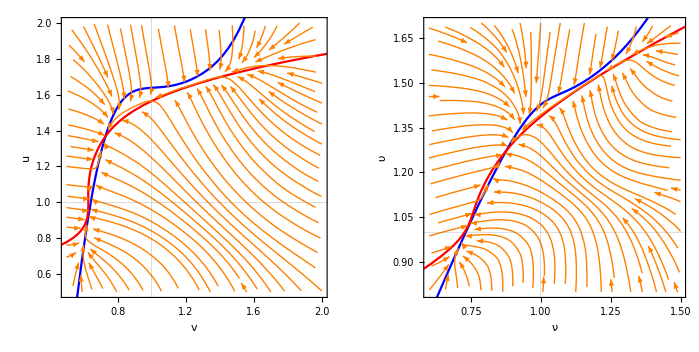

```mathematica
a=1/5;StreamPlotvu[{gnm,gnm},{gnm,gki},{gna,gkv},Subscript[vu, range],Subscript[νυ, range]]
```

Left – Spine-head space: Only one stable point remains (down-up).  
Right – Dendrite-shaft space: Mapping from spine-head {v,u} to dendrite-shaft {ν,υ} space.

### Energy landscape

#### 3-D plot

```mathematica
{νr,υr}={{0.4,1.9},{0.3,2.1}}; δ=0.01;(* plot ranges and point spacing *)
{vr,ur}={{0.1,2.45},{0.1,2.55}}; 
Hr={-0.2,0.15};
valsvu=Flatten[
Table[Hvu[νt,υt],Evaluate@Flatten@{νt,νr,δ},Evaluate@Flatten@{υt,υr,δ}],1];
enervu=Select[valsvu,(vr[[1]]<#[[1]]<vr[[2]])∧(ur[[1]]<#[[2]]<ur[[2]])&];
ListPlot3D[enervu,(* Change ViewPoint by manipulating output *)
PlotRange->{vr,ur,Hr},ClippingStyle->None,AxesLabel->{Style[v,"Output",FontColor->Blue],Style[u,"Output",FontColor->Red]}
]
```

-Graphics3D-

Previous plot:

-Graphics3D-

Redo plot with voltages in millivolts:

```mathematica
dinv[d_]:=60d-120;
{vir,uir}={dinv/@vr,dinv/@ur};
enervumv={dinv[#[[1]]],dinv[#[[2]]],#[[3]]}&/@enervu;
ListPlot3D[enervumv,(* Change ViewPoint by manipulating output *)
PlotRange->{vir,uir,Hr},ClippingStyle->None,AxesLabel->{Style[v,"Output",FontColor->Blue],Style[u,"Output",FontColor->Red]}
]
```

-Graphics3D-

Previous plot:

-Graphics3D-

#### Cross sections

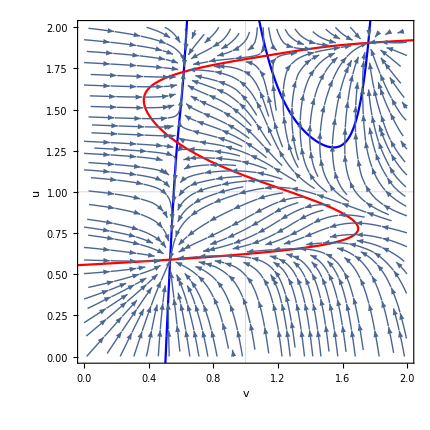

Find rest-rest (rr), rest-plateau (rp), and plateau-plateau (pp) stable points by passing a nearby point {ν0,υ0} to fp[gnp,gip,ν0,υ0]:

```mathematica
({rr,rp,pp}={fp[gnp,gip,νd,νd],fp[gnp,gip,νd,υp],fp[gnp,gip,υp,υp]})//TableForm
```

νt→0.642662 | υt→0.859826 | vs→0.532688 | us→0.588334
νt→0.953359 | υt→1.61876 | vs→0.617048 | us→1.72864
νt→1.65517 | υt→1.85518 | vs→1.75864 | us→1.90427

```mathematica
{rrvu,rpvu,ppvu}={vs,us}/.{rr,rp,pp}
```

{{0.532688,0.588334},{0.617048,1.72864},{1.75864,1.90427}}

Find cross-section parallel to u-axis through the first (rrvu) and second (rpvu) stable point by plotting three candidates:

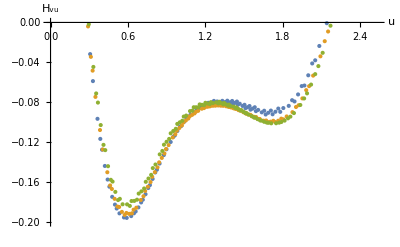

```mathematica
vlist={0.53,0.58,0.62};enerv1u={#⟦2⟧,#[[3]]}&/@Select[valsvu,(ur[[1]]<#[[2]]<ur[[2]])∧(vlist[[1]]-δ<#[[1]]<vlist[[1]]+δ)&];
enerv2u={#⟦2⟧,#[[3]]}&/@Select[valsvu,(ur[[1]]<#[[2]]<ur[[2]])∧(vlist[[2]]-δ<#[[1]]<vlist[[2]]+δ)&];
enerv3u={#⟦2⟧,#[[3]]}&/@Select[valsvu,(ur[[1]]<#[[2]]<ur[[2]])∧(vlist[[3]]-δ<#[[1]]<vlist[[3]]+δ)&];ListPlot[{enerv1u,enerv2u ,enerv3u},PlotRange->{-0.2,0.0},AxesLabel->{u,Subscript[H, vu]}]
```

The orange one (enerv2u) is closest to the minima.

Find cross-section parallel to v-axis through the second (rpvu) and third (ppvu) stable point by plotting three candidates:

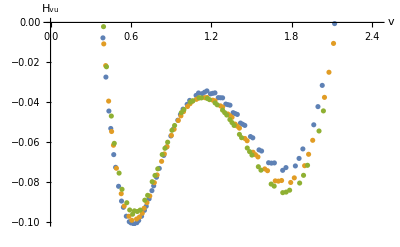

```mathematica
ulist={1.75,1.8,1.85};enervu1={#⟦1⟧,#[[3]]}&/@Select[valsvu,(vr[[1]]<#[[1]]<vr[[2]])∧(ulist[[1]]-δ<#[[2]]<ulist[[1]]+δ)&];
enervu2={#⟦1⟧,#[[3]]}&/@Select[valsvu,(vr[[1]]<#[[1]]<vr[[2]])∧(ulist[[2]]-δ<#[[2]]<ulist[[2]]+δ)&];
enervu3={#⟦1⟧,#[[3]]}&/@Select[valsvu,(vr[[1]]<#[[1]]<vr[[2]])∧(ulist[[3]]-δ<#[[2]]<ulist[[3]]+δ)&];ListPlot[{enervu1,enervu2 ,enervu3},PlotRange->{-0.1,0.0},AxesLabel->{v,Subscript[H, vu]}]
```

The orange one (enervu2) is closest to the minima.

Find cross-section in diagonal direction through first (rrvu) and third (ppvu) stable points:

```mathematica
{Δx,Δy}=ppvu-rrvu; (* vector form first to third stable-point *)
{δx,δy}={δ,(Δy/Δx)δ}; (* vector from one point on plot to the next *)
normal={-δy,δx}/√({-δy,δx}.{-δy,δx}); (* orthogonal unit-vector *)
distance[x_]:=normal.(x-rrvu); (* point x's distance from the cross-section *)
enervudiag3D=Select[valsvu,(-δ<distance[{#[[1]],#[[2]]}]<δ)&];
enervudiag2D={#⟦1⟧,#[[3]]}&/@enervudiag3D; (* projection onto v-axis *)
```

This diagonal cross-section is plotted (green) together with the ones parallel to the u-axis (blue) and v-axis (orange).

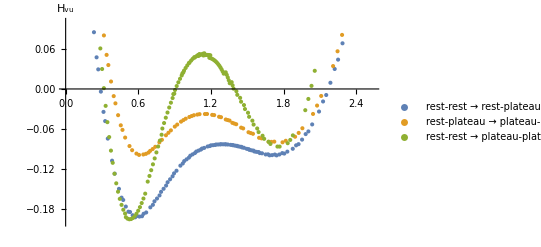

```mathematica
sectionplots=ListPlot[{enerv2u,enervu2,enervudiag2D},
PlotRange->{-0.2,0.1},AxesLabel->{None,Subscript[H, vu]},PlotLegends->{
"rest-rest → rest-plateau","rest-plateau → plateau-plateau","rest-rest → plateau-plateau"}]
```

Find a tenth-order polynomial fit to each cross-section:

```mathematica
enerfits = Fit[#, {1, x, x^2,x^3, x^4,x^5,x^6,x^7,x^8,x^9,x^10}, x]&/@{enerv2u,enervu2,enervudiag2D}
```

{0.600265-2.33274 x-1.32774 x^2+10.3853 x^3-9.24584 x^4-4.64999 x^5+13.6805 x^6-10.583 x^7+4.13027 x^8-0.831546 x^9+0.0687782 x^10,0.791181-3.25644 x+4.42744 x^2-9.98357 x^3+32.8388 x^4-58.7113 x^5+58.1277 x^6-33.9821 x^7+11.7588 x^8-2.23388 x^9+0.179876 x^10,1.04793-2.15226 x-17.4096 x^2+72.5147 x^3-121.833 x^4+117.137 x^5-71.5658 x^6+28.5294 x^7-7.22132 x^8+1.05486 x^9-0.0676552 x^10}

Plot the cross sections and their fits:

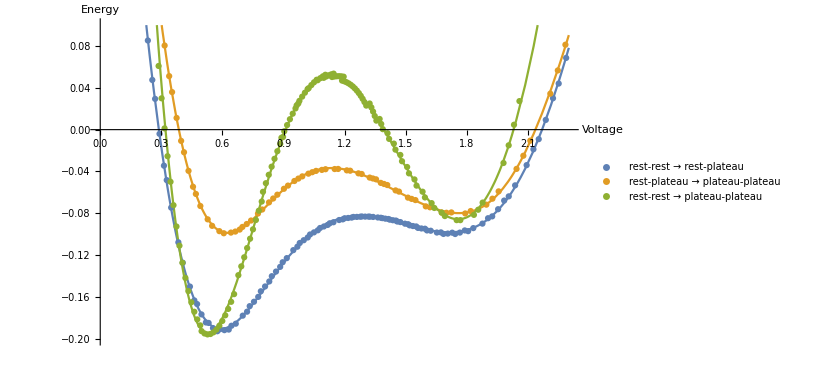

```mathematica
Show[Plot[enerfits,{x,0.2,2.3},PlotRange->{-0.2,0.1}, AxesLabel->{"Voltage","Energy"}],sectionplots]
```

The energy barriers are 0.062, 0.108, and 0.243, from smallest (orange) to largest (green). Thus, flipping a segment from rest to plateau is four times easier (0.243/0.62) when its distal neighbor has been flipped.

### Simulations

We solve u’s and v’s differential equations for various initial conditions.

```mathematica
vuνυeqs={
Subscript[τ, spi] v'[t]==ν[t]-v[t]+Subscript[g, ir] Subscript[f, sig][v[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, v] Subscript[f, sig][v[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[f, v](Subscript[e, exc]-v[t]),
Subscript[τ, m] ν'[t]==v[t]-ν[t]+(l/s)^2(υ[t]-ν[t])+Subscript[g, prox](Subscript[ν, dn]-ν[t])+Subscript[g, ak] Subscript[f, sig][ν[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, Na] Subscript[f, sig][ν[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]],
Subscript[τ, spi] u'[t]==υ[t]-u[t]+Subscript[g, ir] Subscript[f, sig][u[t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, u] Subscript[f, sig][u[t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[f, u](Subscript[e, exc]-u[t]),
Subscript[τ, m] υ'[t]==u[t]-υ[t]+Subscript[g, dist](Subscript[υ, up]-υ[t])+(l/s)^2(ν[t]-υ[t])+Subscript[g, ak] Subscript[f, sig][υ[t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, Na] Subscript[f, sig][υ[t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]};
vuνυbcs={u[0]==us,υ[0]==υt,v[0]==vs,ν[0]==νt}; (* initial conditions *)
pars=rr~Join~{Subscript[υ, up]->υp,Subscript[ν, dn]->νd,Subscript[g, ir]->gip,Subscript[g, Na]->gna,Subscript[g, ak]->gk,Subscript[g, prox]->gprx,Subscript[g, dist]->gdis}; (* assignments *)
(* h and p normalize NMDA and AMPA conductances, respectively — see Synaptic Conductance Waveforms *)
gft={Subscript[g, u]->gnp h α[t,0],Subscript[g, v]-> gnp h α[t,1.0],Subscript[f, u]->Subscript[β, u] p ϵ[t,0],Subscript[f, v]->Subscript[β, v] p ϵ[t,1]}; 
odes=vuνυeqs~Join~vuνυbcs/.pars~Join~gft;
```

We tweaked peak AMPA conductances, β_u for f_v(t) and β_v for f_v(t), to  find the smallest values that trigger transitions between stable points.

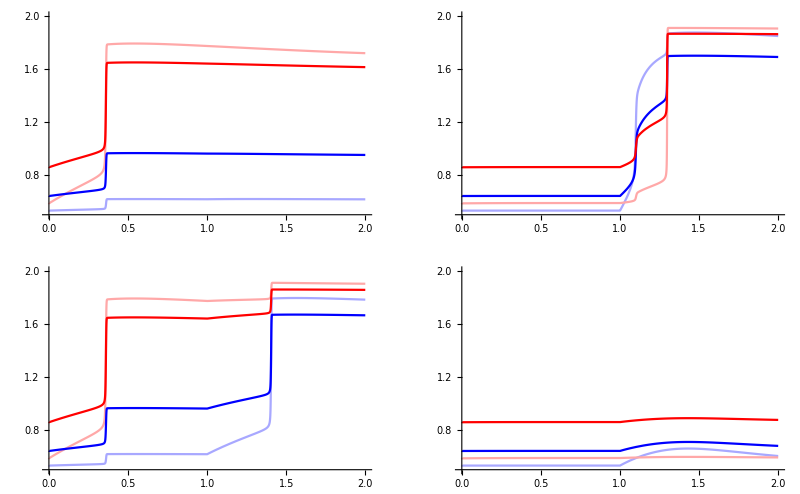

```mathematica
tm=2;(*{υp,νd}={1.925,0.5};gip=3.75;gk=0.005;gnp=0.6;gna=0.65;*)
GraphicsGrid[
Map[
Show[{
sol=NDSolve[odes/.#,{v[t],u[t],ν[t],υ[t]},{t,0,tm}];Plot[Evaluate[{v[t],u[t],ν[t],υ[t]}/.sol],{t,0,tm},PlotRange->{0.5,2.0},
PlotStyle->{Lighter[Blue,0.66],Lighter[Red,0.66],Blue,Red}]
}]&,
{{{Subscript[β, u]->0.2478,Subscript[β, v]->0},{Subscript[β, u]->0,Subscript[β, v]->0.9152}},
{{Subscript[β, u]->0.2478,Subscript[β, v]->0.1705},{Subscript[β, u]->0,Subscript[β, v]->0.268}}},{2}]]
```

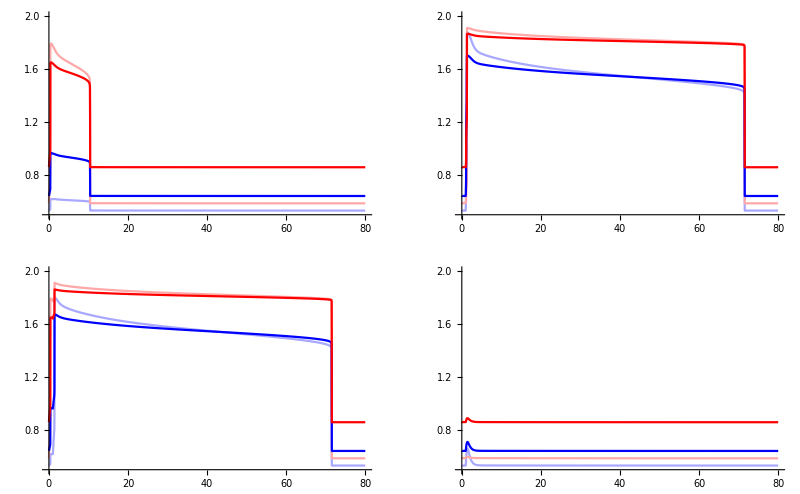

```mathematica
tm=80;
(*{υp,νd}={1.925,0.5};gip=3.75;gk=0.005;gnp=0.6;gna=0.65;*)
GraphicsGrid[
Map[
Show[{
sol=NDSolve[odes/.#,{v[t],u[t],ν[t],υ[t]},{t,0,tm}];Plot[Evaluate[{v[t],u[t],ν[t],υ[t]}/.sol],{t,0,tm},PlotRange->{0.5,2.0},
PlotStyle->{Lighter[Blue,0.66],Lighter[Red,0.66],Blue,Red}]
}]&,
{{{Subscript[β, u]->0.2478,Subscript[β, v]->0},{Subscript[β, u]->0,Subscript[β, v]->0.9152}},
{{Subscript[β, u]->0.2478,Subscript[β, v]->0.1705},{Subscript[β, u]->0,Subscript[β, v]->0.268}}},{2}]]
```

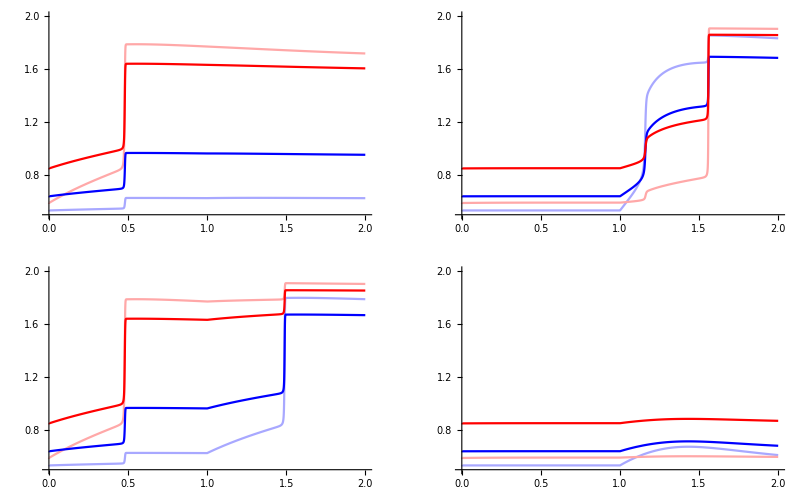

```mathematica
tm=2;
(*{υp,νd}={1.925,0.5};gip=3.5;gk=0.005;gnp=0.6;gna=0.65;*)
GraphicsGrid[
Map[
Show[{
sol=NDSolve[odes/.#,{v[t],u[t],ν[t],υ[t]},{t,0,tm}];Plot[Evaluate[{v[t],u[t],ν[t],υ[t]}/.sol],{t,0,tm},PlotRange->{0.5,2.0},
PlotStyle->{Lighter[Blue,0.66],Lighter[Red,0.66],Blue,Red}]
}]&,
{{{Subscript[β, u]->0.2209,Subscript[β, v]->0},{Subscript[β, u]->0,Subscript[β, v]->0.5979}},
{{Subscript[β, u]->0.2209,Subscript[β, v]->0.1433},{Subscript[β, u]->0,Subscript[β, v]->0.268}}},{2}]]
```

u(t) is red and v(t) is blue: 
Upper-left: β_u ≥ 0.041 triggers down-down to up-up transition (note that u’s left neighbor is up).
Lower-left: β_v = 0.041 fails to trigger down-down to up-up transition, because v’s left neighbor (i.e. u) is down. 
Upper-right: β_v ≥ 0.242 triggers down-down to up-up transition.
Lower-right: β_v ≥ 0.124 triggers up-down to up-up transition—flipping u halves the threshold.

Here the same results plotted on a longer time-scale that shows u’s transition back down.

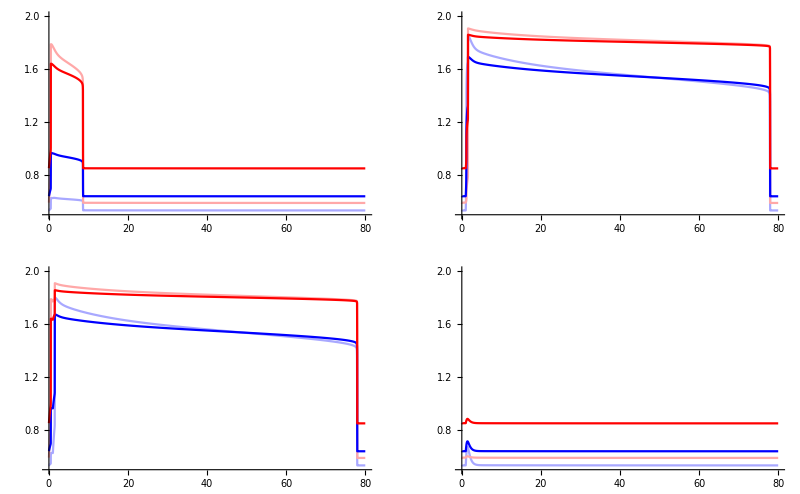

```mathematica
tm=80;
(*{υp,νd}={1.925,0.5};gip=3.5;gk=0.005;gnp=0.6;gna=0.65;*)
GraphicsGrid[
Map[
Show[{
sol=NDSolve[odes/.#,{v[t],u[t],ν[t],υ[t]},{t,0,tm}];Plot[Evaluate[{v[t],u[t],ν[t],υ[t]}/.sol],{t,0,tm},PlotRange->{0.5,2.0},
PlotStyle->{Lighter[Blue,0.66],Lighter[Red,0.66],Blue,Red}]
}]&,
{{{Subscript[β, u]->0.2209,Subscript[β, v]->0},{Subscript[β, u]->0,Subscript[β, v]->0.5979}},
{{Subscript[β, u]->0.2209,Subscript[β, v]->0.1433},{Subscript[β, u]->0,Subscript[β, v]->0.268}}},{2}]]
```

```mathematica
vuνυeqs={
Subscript[τ, spi] u'[t]==(Subscript[g, ir](Subscript[e, kv]-u[t]))/(1+ⅇ^(-(u[t]-Subscript[v, iha])/Subscript[v, isp]))+(Subscript[g, u](Subscript[e, nmda]-u[t]))/(1+ⅇ^(-(u[t]-Subscript[v, nha])/Subscript[v, nsp]))+Subscript[f, u](Subscript[e, ampa]-u[t])+υ[t]-u[t],
Subscript[τ, m] υ'[t]==u[t]-υ[t]+(l/s)^2(Subscript[υ, up]-2υ[t]+ν[t])+(Subscript[g, c](Subscript[e, Ca]-υ[t]))/(1+ⅇ^(-(υ[t]-Subscript[v, cha])/Subscript[v, csp])),Subscript[τ, spi] v'[t]==(Subscript[g, ir](Subscript[e, kv]-v[t]))/(1+ⅇ^(-(v[t]-Subscript[v, iha])/Subscript[v, isp]))+(Subscript[g, v](Subscript[e, nmda]-v[t]))/(1+ⅇ^(-(v[t]-Subscript[v, nha])/Subscript[v, nsp]))+Subscript[f, v](Subscript[e, ampa]-v[t])+ν[t]-v[t],
Subscript[τ, m] ν'[t]==v[t]-ν[t]+(l/s)^2(υ[t]-2ν[t]+Subscript[ν, dn])+(Subscript[g, c](Subscript[e, Ca]-ν[t]))/(1+ⅇ^(-(ν[t]-Subscript[v, cha])/Subscript[v, csp]))};
vuνυbcs={u[0]==u0,υ[0]==υ0,v[0]==v0,ν[0]==ν0};
pars={Subscript[υ, up]->υp,u0->νd,υ0->νd,Subscript[ν, dn]->νd,v0->νd,ν0->νd,Subscript[g, ir]->gip,Subscript[g, c]->gcp};
a= gnp/(h α[t,0]/.tfmax); 
gft={Subscript[g, u]->a h α[t,0],Subscript[g, v]->a h α[t,1.0],Subscript[f, u]->Subscript[β, u] p ϵ[t,0],Subscript[f, v]->Subscript[β, v] p ϵ[t,1]};
odes=vuνυeqs~Join~vuνυbcs/.pars~Join~gft;
```

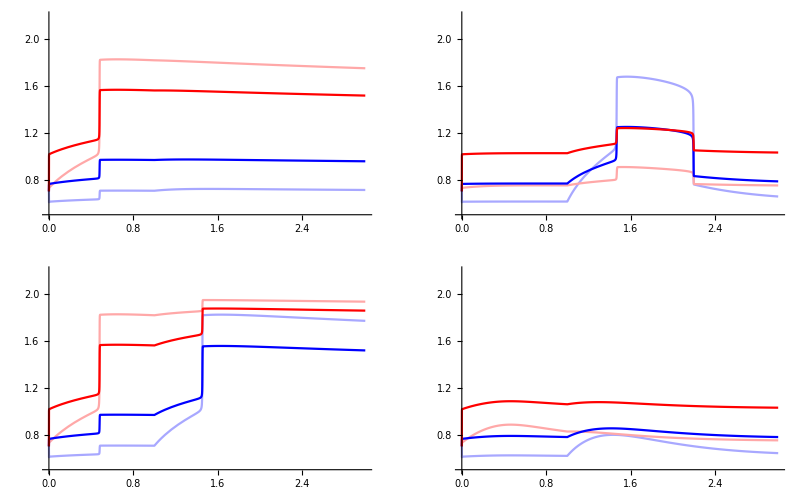

```mathematica
tm=3; (* υν=1.67,νd=0.74,gip=1.25; gnp=1.75; gcp=0.4; 0.65x up-up, 0.55x up-dn *)
GraphicsGrid[
Map[
Show[{
sol=NDSolve[odes/.#,{v[t],u[t],ν[t],υ[t]},{t,0,tm}];Plot[Evaluate[{v[t],u[t],ν[t],υ[t]}/.sol],{t,0,tm},PlotRange->{0.5,2.2},
PlotStyle->{Lighter[Blue,0.66],Lighter[Red,0.66],Blue,Red}]
}]&,
{{{Subscript[β, u]->0.160,Subscript[β, v]->0},{Subscript[β, u]->0,Subscript[β, v]->0.366}},
{{Subscript[β, u]->0.160,Subscript[β, v]->0.186},{Subscript[β, u]->0.119,Subscript[β, v]->0.21}}},{2}]]
```

We find four critical combinations of initial condition and AMPA amplitude (u(t) is red and v(t) is blue): 
Upper-left: β ≥ 4.9 triggers a up-down to up-up transition.
Upper-right: β = 4.9 fails to transition from down-down to up-up.
Lower-left: β ≥ 12.5 triggers a down-down to up-down transition.
Lower-right: β ≥ 13.7 triggers a down-down to up-up transition.

## Stretch of dendrite

We model a stretch of dendrite by breaking it up into a string of compartments, serially connected by axial resistances. Each compartment is equipped with a leak, a Na, a KIR, and an NMDA conductance, as above.

### Coupled segments

```mathematica
T=1; (* interval between input spikes *)
s =3; (* number of slices per segment *)
ss=20; (* number of segments and locations to be swapped *)
time=6ss T;(* simulation time *)
```

```mathematica
vsolv=Table[Subscript[ν, i],{i,0,ss}];
```

```mathematica
veqs:=Join[
{Subscript[τ, spi] Subscript[v, 0]'[t]==Subscript[ν, 0][t]-Subscript[v, 0][t]+0 Subscript[g, ir] Subscript[f, sig][Subscript[v, 0][t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+ Subscript[g, 0] Subscript[f, sig][Subscript[v, 0][t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+p0 Subscript[f, 0](Subscript[e, exc]-Subscript[v, 0][t]),
Subscript[τ, m] Subscript[ν, 0]'[t]==Subscript[v, 0][t]-Subscript[ν, 0][t]+(l/s)^2(Subscript[ν, 1][t]-Subscript[ν, 0][t])+Subscript[g, ak] Subscript[f, sig][Subscript[ν, 0][t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, Na] Subscript[f, sig][Subscript[ν, 0][t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]},Table[Subscript[τ, spi] Subscript[v, i]'[t]==Subscript[ν, i][t]-Subscript[v, i][t]+Subscript[g, ir] Subscript[f, sig][Subscript[v, i][t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, i] Subscript[f, sig][Subscript[v, i][t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[f, i](Subscript[e, exc]-Subscript[v, i][t]),{i,1,ss-1}],
Table[Subscript[τ, m] Subscript[ν, i]'[t]==Subscript[v, i][t]-Subscript[ν, i][t]+(l/s)^2(Subscript[ν, i-1][t]+Subscript[ν, i+1][t]-2 Subscript[ν, i][t])+Subscript[g, ak] Subscript[f, sig][Subscript[ν, i][t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, Na] Subscript[f, sig][Subscript[ν, i][t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]],{i,1,ss-1}],
{Subscript[τ, spi] Subscript[v, ss]'[t]==Subscript[ν, ss][t]-Subscript[v, ss][t]+Subscript[g, ir] Subscript[f, sig][Subscript[v, ss][t],Subscript[e, inh],Subscript[𝔳, iha],Subscript[𝔳, isp]]+Subscript[g, ss] Subscript[f, sig][Subscript[v, ss][t],Subscript[e, exc],Subscript[𝔳, nha],Subscript[𝔳, nsp]]+Subscript[f, ss](Subscript[e, exc]-Subscript[v, ss][t]),
Subscript[τ, m] Subscript[ν, ss]'[t]==Subscript[v, ss][t]-Subscript[ν, ss][t]+(l/s)^2(Subscript[ν, ss-1][t]-Subscript[ν, ss][t])+Subscript[g, ak] Subscript[f, sig][Subscript[ν, ss][t],Subscript[e, inh],Subscript[𝔳, kha],Subscript[𝔳, ksp]]+Subscript[g, Na] Subscript[f, sig][Subscript[ν, ss][t],Subscript[e, Na],Subscript[𝔳, naha],Subscript[𝔳, nasp]]+Subscript[g, den](Subscript[e, inh]-Subscript[ν, ss][t])},
Table[Subscript[v, i][0]==0.5,{i,0,ss}],Table[Subscript[ν, i][0]==0.5,{i,0,ss}]
]/.{Subscript[g, Na]->gna,Subscript[g, ir]->gip,Subscript[g, ak]->gk,Subscript[g, den]->gprx}~Join~init (*0.696 0.19 for s=10*)
```

### Simulation code

Make this a module a called with jitter, noise, steps, swaps, and trails.

```mathematica
(*Subscript[δ, f]=0.8GeometricMean[{0.0807,0.3088}];*)
p0=15;
Subscript[δ, f]=0.25;(*0.17-0.33*)(*0.15-0.275*)(*0.08-0.125*)(*0.06-0.075*)
Subscript[δ, g]=gnp/(h α[t,0]/.tfmax) (*0.65*); (* renamed tpeak *)
kmax=1;dmax=4;jmax=4; 
(*kmax=1;dmax=25;jmax=100;*)
pos=Range[ss];
Subscript[σ, t]=0.0001;Subscript[μ, t]=1.5;Subscript[σ, v]=0.0001;Subscript[μ, v]=1;
For[set={};k=1,k≤kmax,k++,(* jitter sweep *)
For[solns={};data={};dis=0,dis≤dmax,dis++, (* swap sweep *)
For[vals={};trials={};j=1,j≤jmax,j++, (* trials *)
Subscript[Δ, t]=RandomVariate[NormalDistribution[Subscript[μ, t],k Subscript[σ, t]],ss+1];
Subscript[Δ, g]=RandomVariate[NormalDistribution[Subscript[μ, v],k Subscript[σ, v]],ss+1];
Subscript[Δ, f]=RandomVariate[NormalDistribution[Subscript[μ, v],k Subscript[σ, v]],ss+1];
(*Subscript[Δ, q]=RandomVariate[BinomialDistribution[4,4/5],ss+1];*)
cycles=PermutationProduct@@(Cycles[{{#,#+1}}]&/@RandomSample[Drop[pos,-1],dis]);
perm=Permute[pos,cycles];
(* swap, perturb, and jitter Subscript[g, Subscript[NMDA, i]](t) and Subscript[g, Subscript[AMPA, i]](t) *)
(* MapIndexed[(Subscript[g, #2⟦1⟧-1]=Subscript[Δ, g]⟦#1⟧a h α[t,#1-1+Subscript[Δ, t]⟦#1⟧]; Subscript[f, #2⟦1⟧-1]=Subscript[Δ, f]⟦#1⟧b p ϵ[t,#1-1+Subscript[Δ, t]⟦#1⟧] )&,perm]; *)
Subscript[g, 0]=Subscript[Δ, g]⟦1⟧Subscript[δ, g] h α[t,0+Subscript[Δ, t]⟦1⟧];Subscript[f, 0]=Subscript[Δ, f]⟦1⟧Subscript[δ, f] p ϵ[t,0+Subscript[Δ, t]⟦1⟧];
MapIndexed[(Subscript[g, #2⟦1⟧]=Subscript[Δ, g]⟦#1+1⟧Subscript[δ, g] h α[t,#1-1+Subscript[Δ, t]⟦#1+1⟧]; Subscript[f, #2⟦1⟧]=Subscript[Δ, f]⟦#1+1⟧Subscript[δ, f] p ϵ[t,#1-1+Subscript[Δ, t]⟦#1+1⟧] )&,perm]; 
soln=NDSolve[veqs,vsolv,{t,0,time},Method->{"EquationSimplification"->"Residual"}];
AppendTo[trials,soln];
(* find max vpk of voltages in last segment at equally spaced times tpk *)
tpk=Range[0,time,time/ss];
vpk=Max[(vsolv⟦ss+1⟧/.soln⟦1,ss+1⟧)/@tpk]; 
AppendTo[vals,vpk]
];
AppendTo[solns,trials];
(* count how many trials cross dendrite's spike-threshold (x = 2) *)
AppendTo[data,{dis,Plus@@(vals/.{x_/;x>1.5->1,x_/;x≤1.5->0})}]
];
AppendTo[set,data]
]
```

### Test plots

```mathematica
palettes={"CherryTones","LakeColors"};
scheme=Map[(ColorData[#]/@Range[0.95,0.05,-0.9/(ss/2)])&,palettes
]//Transpose//Flatten;
```

Space is on the y-axis and time is on the x-axis

```mathematica
vr={0.5,2.0};
```

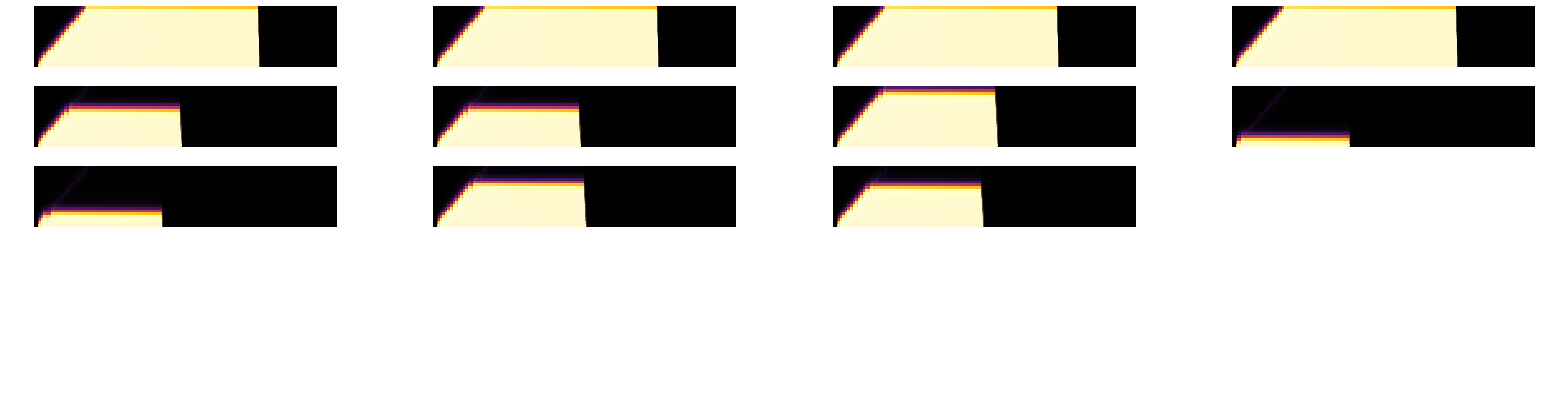

```mathematica
Map[(*{υp,νd}={1.975,0.5};gip=3.0;gk=0.01;gnp=0.85;gna=0.65;*)
ReliefPlot[
Table[(Subscript[ν, i][t]/.#)//First,{i,0,ss},{t,0,time,time/(40ss)}],
ColorFunction->"SunsetColors",PlotRange->vr,Frame->False,AspectRatio->0.2
]&, 
solns,{2}
]//GraphicsGrid
```

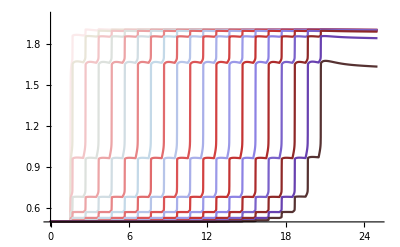

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦1,2⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

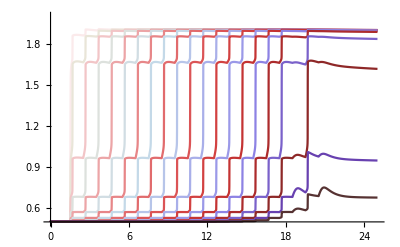

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦2,3⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

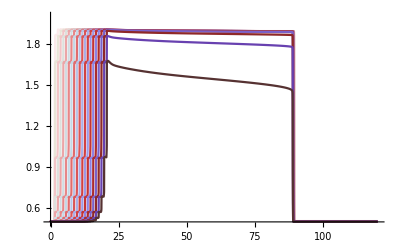

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss}]/.solns⟦1,1⟧],{t,0,time},PlotRange->vr,PlotStyle->scheme]
```

```mathematica
Map[(*{υp,νd}={1.85,0.5};gip=4.5;gk=0.01;gnp=0.865;gcp=0.39;*)
ReliefPlot[
Table[(Subscript[ν, i][t]/.#)//First,{i,0,ss},{t,0,time,time/(40ss)}],
ColorFunction->"SunsetColors",PlotRange->vr,Frame->False,AspectRatio->0.2
]&, 
solns,{2}
]//GraphicsGrid
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦1,2⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦2,3⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss}]/.solns⟦1,1⟧],{t,0,time},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss}]/.solns⟦1,1⟧],{t,0,time},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

### Membrane voltage waveforms

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦1,4⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss} ]/.solns⟦2,4⟧] ,{t,0,25},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss}]/.solns⟦1,4⟧],{t,0,time},PlotRange->vr,PlotStyle->scheme,Axes->None]
```

-Graphics-

```mathematica
Plot[Evaluate[Table[Subscript[ν, i][t],{i,0,ss}]/.solns⟦2,4⟧],{t,0,time},PlotRange->vr,PlotStyle->scheme]
```

-Graphics-